## Initializing

```mathematica
resfinal={{12.900390625,13.8671875},{19.66796875,20.634765625},{28.369140625,29.3359375},{39.00390625,39.970703125},{50.60546875,51.572265625},{64.140625,65.107421875},{78.642578125,79.609375},{96.044921875,97.01171875},{113.447265625,114.4140625},{133.75,134.716796875},{155.01953125,155.986328125},{178.22265625,179.189453125},{202.392578125,203.359375},{228.49609375,229.462890625},{255.56640625,256.533203125},{285.537109375,286.50390625},{315.5078125,316.474609375},{348.37890625,349.345703125},{382.216796875,383.18359375},{417.98828125,418.955078125},{454.7265625,455.693359375},{493.3984375,494.365234375},{533.037109375,534.00390625},{574.609375,575.576171875},{618.115234375,619.08203125},{663.5546875,664.521484375},{709.9609375,710.927734375},{757.333984375,758.30078125},{807.607421875,808.57421875},{858.84765625,859.814453125},{911.0546875,912.021484375},{965.1953125,966.162109375}};
```

Above is from emcmanis_findcriticalvalues.nb. Run with rho_inf = 20*λ.

```mathematica
Critical[λ_,consts_]:=Module[{H,res,dρ,ρinf,nn},
dρ=consts[[1]];
ρinf=Floor[consts[[2]]];
nn=Floor[consts[[3]]];
H=SparseArray[{{n_,n_}->2./dρ^2-2./(n*dρ)ⅇ^(-n*dρ/λ),{n_, m_}/; Abs[n-m] == 1 -> -1./dρ^2},{nn,nn}, 0.];
res=Sort[Eigenvalues[H,-25]];(*Went from 100 down to 25 eigenvalues, which sped this calculation up immensely with no apparent loss of information*)
Return[res]
]
```

```mathematica
CountNegs[list_]:=Module[{neg,i},
neg=0;
For[i=1,list[[i]]<0,i++,
neg++;
];
Return[neg]
]
```

```mathematica
Bisect[F_,consts_,x0_,xf_,ϵ_]:=Module[{mid,val,lnegs,vam,mnegs,ret},
mid=x0+Abs[x0-xf]/2;
Print["Bisecting. Midpoint is "<>ToString[mid]];
val=F[x0,consts];
lnegs=CountNegs[val];
vam=F[mid,consts];
mnegs=CountNegs[vam];
If[xf-x0>ϵ,
(*Print[{lnegs,mnegs},{val[[1]],vam[[1]]}];*)
If[lnegs<mnegs || (lnegs==mnegs && val[[1]] < vam[[1]]), (*if there is a zero on the lower half*)
Return[Bisect[F,consts,x0,mid,ϵ]];, (*bisect it*)
Return[Bisect[F,consts,mid,xf,ϵ]]; (*otherwise try the upper half*)
];,
Return[{mid,mnegs}];
]
]
```

```mathematica
rhoinfs={40};
```

### Junk?

```mathematica
ParallelTable[{i,j,Evaluate[$KernelID],Timing[Bisect[Critical,{0.01,rhoinfs[[j]],rhoinfs[[j]]/0.01},resfinal[[i,1]],resfinal[[i,2]],10.^(-6)]]},{i,1,2},{j,1,3}]
```

Bisecting. Midpoint is 13.3838

Bisecting. Midpoint is 20.1514

```mathematica
Parallelize[Table[i,{i,1,10}]]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
lcs=Parallelize[Table[Table[{j,Bisect[Critical,{0.01,rhoinfs[[j]],rhoinfs[[j]]/0.01},resfinal[[i,1]],resfinal[[i,2]],10^(-6)]},{j,1,3}],{i,1,Length[resfinal]}]];
```

```mathematica
ParallelTable[i+2,{i,1,10}]
```

{3,4,5,6,7,8,9,10,11,12}

### Disappearing Eigenvalues

```mathematica
evs={}
```

{}

```mathematica
Bisect[Critical,{0.1,400.,400./0.1}, 18.66796875,21.634765625`+1,10^(-6)]
```

Bisecting. Midpoint is 20.1514

Bisecting. Midpoint is 20.8931

Bisecting. Midpoint is 20.5222

Bisecting. Midpoint is 20.3368

Bisecting. Midpoint is 20.2441

Bisecting. Midpoint is 20.1977

Bisecting. Midpoint is 20.1745

Bisecting. Midpoint is 20.163

Bisecting. Midpoint is 20.1572

Bisecting. Midpoint is 20.1601

Bisecting. Midpoint is 20.1615

Bisecting. Midpoint is 20.1622

Bisecting. Midpoint is 20.1626

Bisecting. Midpoint is 20.1628

Bisecting. Midpoint is 20.1629

Bisecting. Midpoint is 20.1628

Bisecting. Midpoint is 20.1628

Bisecting. Midpoint is 20.1628

«5 more identical outputs»

{20.1628,2}

```mathematica
evs
```

```mathematica
evs=Sort[evs];
```

```mathematica
lowests=Table[{evs[[i,1]],evs[[i,2,1]]},{i,1,Length[evs]}]
```

{{18.668,-0.0352544},{20.1514,-0.0390507},{20.1514,-0.0390507},{20.8931,-0.00722268},{20.1514,-0.0390507},{20.5222,-0.0067885},{20.1514,-0.0390507},{20.3368,-0.0395017},{20.1514,-0.0390507},{20.2441,-0.0392768},{20.1514,-0.0390507},{20.1977,-0.0391639},{20.1514,-0.0390507},{20.1745,-0.0391073},{20.1514,-0.0390507},{20.163,-0.039079},{20.1514,-0.0390507},{20.1572,-0.0390649},{20.1572,-0.0390649},{20.1601,-0.0390719},{20.1601,-0.0390719},{20.1615,-0.0390755},{20.1615,-0.0390755},{20.1622,-0.0390773},{20.1622,-0.0390773},{20.1626,-0.0390781},{20.1626,-0.0390781},{20.1628,-0.0390786},{20.1628,-0.0390786},{20.1629,-0.0390788},{20.1628,-0.0390786},{20.1628,-0.0390787},{20.1628,-0.0390786},{20.1628,-0.0390786},{20.1628,-0.0390786},{20.1628,-0.0390787},{20.1628,-0.0390787},{20.1628,-0.0390787},{20.1628,-0.0390787},{20.1628,-0.0390787},{20.1628,-0.0390787},{20.1628,-0.0390787},{20.1628,-0.0390787},{20.1628,-0.0390787},{20.1628,-0.0390787},{20.1628,-0.0390787}}

```mathematica
Sort[lowests]
```

{{18.668,-0.0352544},{20.1514,-0.0390507},{20.1514,-0.0390507},{20.1514,-0.0390507},{20.1514,-0.0390507},{20.1514,-0.0390507},{20.1514,-0.0390507},{20.1514,-0.0390507},{20.1514,-0.0390507},{20.1514,-0.0390507},{20.1572,-0.0390649},{20.1572,-0.0390649},{20.1601,-0.0390719},{20.1601,-0.0390719},{20.1615,-0.0390755},{20.1615,-0.0390755},{20.1622,-0.0390773},{20.1622,-0.0390773},{20.1626,-0.0390781},{20.1626,-0.0390781},{20.1628,-0.0390786},{20.1628,-0.0390786},{20.1628,-0.0390786},{20.1628,-0.0390786},{20.1628,-0.0390786},{20.1628,-0.0390786},{20.1628,-0.0390787},{20.1628,-0.0390787},{20.1628,-0.0390787},{20.1628,-0.0390787},{20.1628,-0.0390787},{20.1628,-0.0390787},{20.1628,-0.0390787},{20.1628,-0.0390787},{20.1628,-0.0390787},{20.1628,-0.0390787},{20.1628,-0.0390787},{20.1628,-0.0390787},{20.1629,-0.0390788},{20.163,-0.039079},{20.1745,-0.0391073},{20.1977,-0.0391639},{20.2441,-0.0392768},{20.3368,-0.0395017},{20.5222,-0.0067885},{20.8931,-0.00722268}}

```mathematica
nos=Table[CountNegs[evs[[i,2]]],{i,1,Length[evs]}]
```

{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,3,3,3,3,3,3,3,3,2,2}

```mathematica
?Sort
```

Sort[list] sorts the elements of list into canonical order. 
Sort[list,p] sorts using the ordering function p.

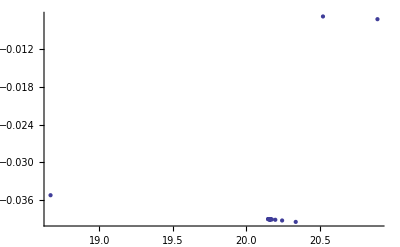

```mathematica
ListPlot[lowests]
```

```mathematica
plotevs=Table[Table[{evs[[j,1]],evs[[j,2,i]]},{i,1,Length[evs[[j,2]]]}],{j,1,Length[evs]}];
```

```mathematica
plotevs = Flatten[plotevs,1];
```

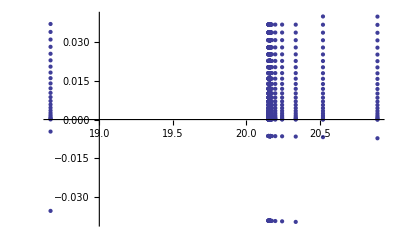

```mathematica
ListPlot[plotevs,PlotRange->Full]
```

```mathematica
Bisect[F_,consts_,x0_,xf_,ϵ_]:=Module[{mid,val,lnegs,vam,mnegs,ret},
mid=x0+Abs[x0-xf]/2;
Print["Bisecting. Midpoint is "<>ToString[mid]];
val=F[x0,consts];
lnegs=CountNegs[val];
vam=F[mid,consts];
mnegs=CountNegs[vam];
evs=Append[evs,{x0,val}];
evs=Append[evs,{mid,vam}];
If[xf-x0>ϵ,
(*Print[{lnegs,mnegs},{val[[1]],vam[[1]]}];*)
If[lnegs<mnegs || (lnegs==mnegs && val[[1]] < vam[[1]]),
Return[Bisect[F,consts,x0,mid,ϵ]];,
Return[Bisect[F,consts,mid,xf,ϵ]];
];,
Return[{mid,mnegs}];
]
]
```

## The Actual Computation

### Computing (TAKES A LONG TIME DO NOT EVALUATE)

{tag, rhoinf, lambda1, lambda2} = > {tag, lc[rhoinf]} <- format of this function below me. This opaque mess massages the data into something easily parallelized.

```mathematica
inputs=Table[Table[{j,rhoinfs[[j]]*resfinal[[i,1]],resfinal[[i,1]]-2,resfinal[[i,2]]+2},{j,1,1}],{i,1,Floor[Length[resfinal]]}]
```

{{{1,516.016,10.9004,15.8672}},{{1,786.719,17.668,22.6348}},{{1,1134.77,26.3691,31.3359}},{{1,1560.16,37.0039,41.9707}},{{1,2024.22,48.6055,53.5723}},{{1,2565.63,62.1406,67.1074}},{{1,3145.7,76.6426,81.6094}},{{1,3841.8,94.0449,99.0117}},{{1,4537.89,111.447,116.414}},{{1,5350.,131.75,136.717}},{{1,6200.78,153.02,157.986}},{{1,7128.91,176.223,181.189}},{{1,8095.7,200.393,205.359}},{{1,9139.84,226.496,231.463}},{{1,10222.7,253.566,258.533}},{{1,11421.5,283.537,288.504}},{{1,12620.3,313.508,318.475}},{{1,13935.2,346.379,351.346}},{{1,15288.7,380.217,385.184}},{{1,16719.5,415.988,420.955}},{{1,18189.1,452.727,457.693}},{{1,19735.9,491.398,496.365}},{{1,21321.5,531.037,536.004}},{{1,22984.4,572.609,577.576}},{{1,24724.6,616.115,621.082}},{{1,26542.2,661.555,666.521}},{{1,28398.4,707.961,712.928}},{{1,30293.4,755.334,760.301}},{{1,32304.3,805.607,810.574}},{{1,34353.9,856.848,861.814}},{{1,36442.2,909.055,914.021}},{{1,38607.8,963.195,968.162}}}

```mathematica
inputs=Flatten[inputs,1]
```

{{1,516.016,10.9004,15.8672},{1,786.719,17.668,22.6348},{1,1134.77,26.3691,31.3359},{1,1560.16,37.0039,41.9707},{1,2024.22,48.6055,53.5723},{1,2565.63,62.1406,67.1074},{1,3145.7,76.6426,81.6094},{1,3841.8,94.0449,99.0117},{1,4537.89,111.447,116.414},{1,5350.,131.75,136.717},{1,6200.78,153.02,157.986},{1,7128.91,176.223,181.189},{1,8095.7,200.393,205.359},{1,9139.84,226.496,231.463},{1,10222.7,253.566,258.533},{1,11421.5,283.537,288.504},{1,12620.3,313.508,318.475},{1,13935.2,346.379,351.346},{1,15288.7,380.217,385.184},{1,16719.5,415.988,420.955},{1,18189.1,452.727,457.693},{1,19735.9,491.398,496.365},{1,21321.5,531.037,536.004},{1,22984.4,572.609,577.576},{1,24724.6,616.115,621.082},{1,26542.2,661.555,666.521},{1,28398.4,707.961,712.928},{1,30293.4,755.334,760.301},{1,32304.3,805.607,810.574},{1,34353.9,856.848,861.814},{1,36442.2,909.055,914.021},{1,38607.8,963.195,968.162}}

```mathematica
inputs[[1]]
```

{1,516.016,10.9004,15.8672}

```mathematica
Findlc[input_,i_,eps_]:=Module[{val,vah,lnegs,hnegs,res},
Print["***Beginning to calculate the "<>ToString[Ceiling[i,2]/2]<>"th lambda, part "<>ToString[input[[1]]]];
val=Critical[input[[3]],{0.1,input[[2]],input[[2]]/0.1}];
vah=Critical[input[[4]],{0.1,input[[2]],input[[2]]/0.1}];
lnegs=CountNegs[val];
hnegs=CountNegs[vah];
If[lnegs<hnegs || (lnegs==hnegs && val[[1]]<vah[[1]]),(*doublechecks for zero*)
Print["Pass!"];
res={input[[1]],Bisect[Critical,{0.1,input[[2]],input[[2]]/0.1},input[[3]],input[[4]],eps]};
,(*else*)
Print["Fail!"];
res={input[[1]],Null};
];
Return[res]
]
```

```mathematica
DistributeDefinitions[Findlc,Bisect,Critical,CountNegs,inputs]
```

```mathematica
refinement=ParallelTable[Findlc[inputs[[i]],i,0.25],{i,1,Length[inputs]}]
```

***Beginning to calculate the 2th lambda, part 1

***Beginning to calculate the 4th lambda, part 1

***Beginning to calculate the 5th lambda, part 1

***Beginning to calculate the 1th lambda, part 1

Pass!

Bisecting. Midpoint is 13.3838

Bisecting. Midpoint is 12.1421

Bisecting. Midpoint is 12.7629

Pass!

Bisecting. Midpoint is 39.4873

Bisecting. Midpoint is 13.0734

Bisecting. Midpoint is 12.9182

Bisecting. Midpoint is 12.8405

***Beginning to calculate the 1th lambda, part 1

Bisecting. Midpoint is 38.2456

Pass!

Bisecting. Midpoint is 79.126

Pass!

Bisecting. Midpoint is 20.1514

Bisecting. Midpoint is 18.9097

Bisecting. Midpoint is 38.8665

Bisecting. Midpoint is 19.5305

Bisecting. Midpoint is 19.8409

Bisecting. Midpoint is 39.1769

Bisecting. Midpoint is 19.9962

Bisecting. Midpoint is 19.9185

Bisecting. Midpoint is 77.8843

Bisecting. Midpoint is 39.0217

Pass!

Bisecting. Midpoint is 134.233

***Beginning to calculate the 2th lambda, part 1

Pass!

Bisecting. Midpoint is 28.8525

Bisecting. Midpoint is 38.9441

Bisecting. Midpoint is 27.6108

***Beginning to calculate the 3th lambda, part 1

Bisecting. Midpoint is 78.5051

Bisecting. Midpoint is 28.2317

Bisecting. Midpoint is 28.5421

Pass!

Bisecting. Midpoint is 51.0889

Bisecting. Midpoint is 28.6973

Bisecting. Midpoint is 28.6197

Bisecting. Midpoint is 78.8156

Bisecting. Midpoint is 49.8472

Bisecting. Midpoint is 132.992

***Beginning to calculate the 7th lambda, part 1

Bisecting. Midpoint is 50.468

Bisecting. Midpoint is 78.9708

Bisecting. Midpoint is 50.7784

Bisecting. Midpoint is 50.6232

Bisecting. Midpoint is 79.0484

Bisecting. Midpoint is 133.613

Bisecting. Midpoint is 50.7008

Pass!

Bisecting. Midpoint is 202.876

***Beginning to calculate the 4th lambda, part 1

***Beginning to calculate the 3th lambda, part 1

Pass!

Bisecting. Midpoint is 64.624

Bisecting. Midpoint is 133.302

Pass!

Bisecting. Midpoint is 96.5283

Bisecting. Midpoint is 63.3823

Bisecting. Midpoint is 201.634

Bisecting. Midpoint is 64.0032

Bisecting. Midpoint is 95.2866

Bisecting. Midpoint is 64.3136

Bisecting. Midpoint is 133.457

Bisecting. Midpoint is 95.9075

Bisecting. Midpoint is 64.1584

Bisecting. Midpoint is 202.255

Bisecting. Midpoint is 64.0808

Bisecting. Midpoint is 95.597

***Beginning to calculate the 8th lambda, part 1

Bisecting. Midpoint is 133.535

Bisecting. Midpoint is 95.7523

Bisecting. Midpoint is 95.6747

Bisecting. Midpoint is 201.945

***Beginning to calculate the 6th lambda, part 1

***Beginning to calculate the 5th lambda, part 1

Pass!

Bisecting. Midpoint is 286.021

Pass!

Bisecting. Midpoint is 113.931

Bisecting. Midpoint is 201.789

Pass!

Bisecting. Midpoint is 155.503

Bisecting. Midpoint is 112.689

Bisecting. Midpoint is 113.31

Bisecting. Midpoint is 154.261

Bisecting. Midpoint is 201.867

Bisecting. Midpoint is 284.779

Bisecting. Midpoint is 113.62

Bisecting. Midpoint is 154.882

Bisecting. Midpoint is 113.775

Bisecting. Midpoint is 113.853

***Beginning to calculate the 7th lambda, part 1

Bisecting. Midpoint is 154.572

Bisecting. Midpoint is 284.158

***Beginning to calculate the 10th lambda, part 1

Pass!

Bisecting. Midpoint is 228.979

Bisecting. Midpoint is 154.727

Bisecting. Midpoint is 154.649

Bisecting. Midpoint is 227.738

Bisecting. Midpoint is 284.468

***Beginning to calculate the 6th lambda, part 1

Pass!

Bisecting. Midpoint is 382.7

Bisecting. Midpoint is 228.359

Pass!

Bisecting. Midpoint is 178.706

Bisecting. Midpoint is 284.624

Bisecting. Midpoint is 177.464

Bisecting. Midpoint is 381.458

Bisecting. Midpoint is 228.048

Bisecting. Midpoint is 178.085

Bisecting. Midpoint is 284.546

Bisecting. Midpoint is 177.775

Bisecting. Midpoint is 227.893

***Beginning to calculate the 9th lambda, part 1

Bisecting. Midpoint is 177.62

Bisecting. Midpoint is 380.838

Bisecting. Midpoint is 227.971

Bisecting. Midpoint is 177.542

Pass!

Bisecting. Midpoint is 315.991

***Beginning to calculate the 8th lambda, part 1

***Beginning to calculate the 11th lambda, part 1

Bisecting. Midpoint is 381.148

Pass!

Bisecting. Midpoint is 256.05

Bisecting. Midpoint is 314.75

Bisecting. Midpoint is 381.303

Bisecting. Midpoint is 254.808

Pass!

Bisecting. Midpoint is 493.882

Bisecting. Midpoint is 315.37

Bisecting. Midpoint is 255.429

Bisecting. Midpoint is 381.381

Bisecting. Midpoint is 315.06

Bisecting. Midpoint is 255.739

Bisecting. Midpoint is 492.64

Bisecting. Midpoint is 255.584

Bisecting. Midpoint is 315.215

***Beginning to calculate the 10th lambda, part 1

Bisecting. Midpoint is 492.019

Bisecting. Midpoint is 255.507

Bisecting. Midpoint is 315.293

***Beginning to calculate the 13th lambda, part 1

Pass!

Bisecting. Midpoint is 418.472

Bisecting. Midpoint is 492.33

***Beginning to calculate the 9th lambda, part 1

Pass!

Bisecting. Midpoint is 618.599

Bisecting. Midpoint is 417.23

Pass!

Bisecting. Midpoint is 348.862

Bisecting. Midpoint is 492.174

Bisecting. Midpoint is 416.609

Bisecting. Midpoint is 347.621

Bisecting. Midpoint is 617.357

Bisecting. Midpoint is 492.252

Bisecting. Midpoint is 416.92

Bisecting. Midpoint is 347.

Bisecting. Midpoint is 416.764

***Beginning to calculate the 12th lambda, part 1

Bisecting. Midpoint is 347.31

Bisecting. Midpoint is 616.736

Pass!

Bisecting. Midpoint is 533.521

Bisecting. Midpoint is 416.687

Bisecting. Midpoint is 347.465

Bisecting. Midpoint is 617.047

Bisecting. Midpoint is 532.279

Bisecting. Midpoint is 347.543

***Beginning to calculate the 11th lambda, part 1

Bisecting. Midpoint is 532.9

Bisecting. Midpoint is 617.202

***Beginning to calculate the 14th lambda, part 1

Pass!

Bisecting. Midpoint is 455.21

Bisecting. Midpoint is 532.589

Bisecting. Midpoint is 453.968

Bisecting. Midpoint is 617.279

Pass!

Bisecting. Midpoint is 710.444

Bisecting. Midpoint is 532.434

Bisecting. Midpoint is 453.347

***Beginning to calculate the 13th lambda, part 1

Bisecting. Midpoint is 453.658

Bisecting. Midpoint is 709.203

Bisecting. Midpoint is 532.356

Pass!

Bisecting. Midpoint is 664.038

Bisecting. Midpoint is 453.813

***Beginning to calculate the 12th lambda, part 1

Bisecting. Midpoint is 708.582

Bisecting. Midpoint is 453.735

Bisecting. Midpoint is 662.796

Pass!

Bisecting. Midpoint is 575.093

Bisecting. Midpoint is 708.271

***Beginning to calculate the 15th lambda, part 1

Bisecting. Midpoint is 662.176

Bisecting. Midpoint is 573.851

Bisecting. Midpoint is 708.427

Bisecting. Midpoint is 574.472

Bisecting. Midpoint is 661.865

Pass!

Bisecting. Midpoint is 808.091

Bisecting. Midpoint is 574.161

Bisecting. Midpoint is 708.504

Bisecting. Midpoint is 662.02

Bisecting. Midpoint is 806.849

Bisecting. Midpoint is 574.006

***Beginning to calculate the 14th lambda, part 1

Bisecting. Midpoint is 662.098

Bisecting. Midpoint is 573.929

Bisecting. Midpoint is 806.228

***Beginning to calculate the 16th lambda, part 1

Pass!

Bisecting. Midpoint is 757.817

Bisecting. Midpoint is 805.918

Pass!

Bisecting. Midpoint is 911.538

Bisecting. Midpoint is 756.576

Bisecting. Midpoint is 806.073

Bisecting. Midpoint is 910.296

Bisecting. Midpoint is 755.955

Bisecting. Midpoint is 805.995

Bisecting. Midpoint is 909.676

Bisecting. Midpoint is 756.265

***Beginning to calculate the 15th lambda, part 1

Bisecting. Midpoint is 756.42

Bisecting. Midpoint is 909.986

Bisecting. Midpoint is 756.343

Pass!

Bisecting. Midpoint is 859.331

Bisecting. Midpoint is 909.831

Bisecting. Midpoint is 858.089

Bisecting. Midpoint is 909.753

Bisecting. Midpoint is 857.469

***Beginning to calculate the 16th lambda, part 1

Bisecting. Midpoint is 857.158

Pass!

Bisecting. Midpoint is 965.679

Bisecting. Midpoint is 857.003

Bisecting. Midpoint is 964.437

Bisecting. Midpoint is 857.08

Bisecting. Midpoint is 963.816

Bisecting. Midpoint is 964.127

Bisecting. Midpoint is 963.971

Bisecting. Midpoint is 963.894

{{1,{12.8405,2}},{1,{19.9185,1}},{1,{28.6197,1}},{1,{38.9441,2}},{1,{50.7008,1}},{1,{64.0808,1}},{1,{79.0484,1}},{1,{95.6747,2}},{1,{113.853,2}},{1,{133.535,2}},{1,{154.649,1}},{1,{177.542,1}},{1,{201.867,1}},{1,{227.971,2}},{1,{255.507,2}},{1,{284.546,1}},{1,{315.293,2}},{1,{347.543,2}},{1,{381.381,2}},{1,{416.687,1}},{1,{453.735,2}},{1,{492.252,2}},{1,{532.356,2}},{1,{573.929,1}},{1,{617.279,2}},{1,{662.098,2}},{1,{708.504,2}},{1,{756.343,1}},{1,{805.995,2}},{1,{857.08,2}},{1,{909.753,2}},{1,{963.894,1}}}

```mathematica
rhoinfs={80}
```

{80}

This one was done with rhoinf = 40, delta = 1/4.

```mathematica
refinement
```

{{1,{12.8405,2}},{1,{19.9185,1}},{1,{28.6197,1}},{1,{38.9441,2}},{1,{50.7008,1}},{1,{64.0808,1}},{1,{79.0484,1}},{1,{95.6747,2}},{1,{113.853,2}},{1,{133.535,2}},{1,{154.649,1}},{1,{177.542,1}},{1,{201.867,1}},{1,{227.971,2}},{1,{255.507,2}},{1,{284.546,1}},{1,{315.293,2}},{1,{347.543,2}},{1,{381.381,2}},{1,{416.687,1}},{1,{453.735,2}},{1,{492.252,2}},{1,{532.356,2}},{1,{573.929,1}},{1,{617.279,2}},{1,{662.098,2}},{1,{708.504,2}},{1,{756.343,1}},{1,{805.995,2}},{1,{857.08,2}},{1,{909.753,2}},{1,{963.894,1}}}

```mathematica
refinement[[1,2,1]]
```

12.7348

```mathematica
deletes={};
For[i=1,i≤11,i++,
deletes=Append[deletes,{i}];
];
```

```mathematica
deletes
```

{{1},{2},{3},{4},{5},{6},{7},{8},{9},{10},{11}}

```mathematica
news=refinement;
```

```mathematica
rhoinfs={80}
```

{80}

```mathematica
newinputs=Table[Table[{j,rhoinfs[[j]]*news[[i,2,1]],news[[i,2,1]]-0.75,news[[i,2,1]]+0.75},{j,1,1}],{i,1,Floor[Length[news]]}];
```

```mathematica
newinputs
```

{{{1,1027.24,12.0905,13.5905}},{{1,1593.48,19.1685,20.6685}},{{1,2289.58,27.8697,29.3697}},{{1,3115.52,38.1941,39.6941}},{{1,4056.07,49.9508,51.4508}},{{1,5126.46,63.3308,64.8308}},{{1,6323.87,78.2984,79.7984}},{{1,7653.97,94.9247,96.4247}},{{1,9108.24,113.103,114.603}},{{1,10682.8,132.785,134.285}},{{1,12371.9,153.899,155.399}},{{1,14203.4,176.792,178.292}},{{1,16149.4,201.117,202.617}},{{1,18237.6,227.221,228.721}},{{1,20440.5,254.757,256.257}},{{1,22763.7,283.796,285.296}},{{1,25223.4,314.543,316.043}},{{1,27803.4,346.793,348.293}},{{1,30510.5,380.631,382.131}},{{1,33334.9,415.937,417.437}},{{1,36298.8,452.985,454.485}},{{1,39380.2,491.502,493.002}},{{1,42588.5,531.606,533.106}},{{1,45914.3,573.179,574.679}},{{1,49382.3,616.529,618.029}},{{1,52967.8,661.348,662.848}},{{1,56680.3,707.754,709.254}},{{1,60507.4,755.593,757.093}},{{1,64479.6,805.245,806.745}},{{1,68566.4,856.33,857.83}},{{1,72780.3,909.003,910.503}},{{1,77111.5,963.144,964.644}}}

```mathematica
newinputs=Flatten[newinputs,1];
```

```mathematica
DistributeDefinitions[newinputs]
```

```mathematica
refinement2=ParallelTable[Findlc[newinputs[[i]],i,1/32.],{i,1,Length[newinputs]}]
```

***Beginning to calculate the 1th lambda, part 1

***Beginning to calculate the 2th lambda, part 1

***Beginning to calculate the 4th lambda, part 1

***Beginning to calculate the 5th lambda, part 1

Pass!

Bisecting. Midpoint is 12.8405

Bisecting. Midpoint is 12.4655

Bisecting. Midpoint is 12.653

Bisecting. Midpoint is 12.7468

Pass!

Bisecting. Midpoint is 38.9441

Bisecting. Midpoint is 12.7937

Bisecting. Midpoint is 12.7702

Bisecting. Midpoint is 12.7585

***Beginning to calculate the 1th lambda, part 1

Pass!

Bisecting. Midpoint is 19.9185

Bisecting. Midpoint is 38.5691

Pass!

Bisecting. Midpoint is 79.0484

Bisecting. Midpoint is 19.5435

Bisecting. Midpoint is 19.731

Bisecting. Midpoint is 19.8248

Bisecting. Midpoint is 38.7566

Bisecting. Midpoint is 19.8717

Pass!

Bisecting. Midpoint is 133.535

Bisecting. Midpoint is 19.8482

Bisecting. Midpoint is 19.86

Bisecting. Midpoint is 38.8503

***Beginning to calculate the 2th lambda, part 1

Bisecting. Midpoint is 78.6734

Pass!

Bisecting. Midpoint is 28.6197

Bisecting. Midpoint is 38.8034

Bisecting. Midpoint is 28.2447

Bisecting. Midpoint is 28.4322

Bisecting. Midpoint is 38.78

Bisecting. Midpoint is 78.8609

Bisecting. Midpoint is 28.526

Bisecting. Midpoint is 133.16

Bisecting. Midpoint is 38.7683

Bisecting. Midpoint is 28.5728

Bisecting. Midpoint is 28.5494

***Beginning to calculate the 3th lambda, part 1

Bisecting. Midpoint is 78.9546

Bisecting. Midpoint is 28.5377

Pass!

Bisecting. Midpoint is 50.7008

***Beginning to calculate the 7th lambda, part 1

Bisecting. Midpoint is 78.9077

Bisecting. Midpoint is 133.347

Bisecting. Midpoint is 50.3258

Bisecting. Midpoint is 50.5133

Bisecting. Midpoint is 50.6071

Bisecting. Midpoint is 78.9312

Bisecting. Midpoint is 133.254

Bisecting. Midpoint is 50.5602

Bisecting. Midpoint is 78.9195

Bisecting. Midpoint is 50.5836

Pass!

Bisecting. Midpoint is 201.867

Bisecting. Midpoint is 50.5719

***Beginning to calculate the 4th lambda, part 1

Bisecting. Midpoint is 133.207

***Beginning to calculate the 3th lambda, part 1

Pass!

Bisecting. Midpoint is 64.0808

Pass!

Bisecting. Midpoint is 95.6747

Bisecting. Midpoint is 133.183

Bisecting. Midpoint is 63.7058

Bisecting. Midpoint is 201.492

Bisecting. Midpoint is 95.2997

Bisecting. Midpoint is 63.8933

Bisecting. Midpoint is 133.195

Bisecting. Midpoint is 63.987

Bisecting. Midpoint is 95.4872

Bisecting. Midpoint is 63.9402

Bisecting. Midpoint is 201.68

***Beginning to calculate the 6th lambda, part 1

Bisecting. Midpoint is 95.3934

Bisecting. Midpoint is 63.9636

Bisecting. Midpoint is 63.9519

Bisecting. Midpoint is 95.4403

Pass!

Bisecting. Midpoint is 154.649

***Beginning to calculate the 8th lambda, part 1

Bisecting. Midpoint is 95.4168

Bisecting. Midpoint is 201.586

Bisecting. Midpoint is 95.4286

Bisecting. Midpoint is 154.274

***Beginning to calculate the 5th lambda, part 1

Bisecting. Midpoint is 154.462

Pass!

Bisecting. Midpoint is 284.546

Bisecting. Midpoint is 201.633

Pass!

Bisecting. Midpoint is 113.853

Bisecting. Midpoint is 154.368

Bisecting. Midpoint is 113.478

Bisecting. Midpoint is 201.609

Bisecting. Midpoint is 284.171

Bisecting. Midpoint is 113.666

Bisecting. Midpoint is 154.415

Bisecting. Midpoint is 113.572

Bisecting. Midpoint is 154.438

Bisecting. Midpoint is 201.598

Bisecting. Midpoint is 283.983

Bisecting. Midpoint is 113.525

Bisecting. Midpoint is 154.427

Bisecting. Midpoint is 113.548

***Beginning to calculate the 7th lambda, part 1

Bisecting. Midpoint is 284.077

***Beginning to calculate the 6th lambda, part 1

Bisecting. Midpoint is 113.537

***Beginning to calculate the 10th lambda, part 1

Pass!

Bisecting. Midpoint is 227.971

Pass!

Bisecting. Midpoint is 177.542

Bisecting. Midpoint is 284.124

Bisecting. Midpoint is 177.167

Bisecting. Midpoint is 227.596

Bisecting. Midpoint is 284.148

Bisecting. Midpoint is 177.354

Pass!

Bisecting. Midpoint is 381.381

Bisecting. Midpoint is 227.408

Bisecting. Midpoint is 177.261

Bisecting. Midpoint is 284.159

Bisecting. Midpoint is 177.214

Bisecting. Midpoint is 227.502

***Beginning to calculate the 9th lambda, part 1

Bisecting. Midpoint is 177.237

Bisecting. Midpoint is 381.006

Bisecting. Midpoint is 227.549

Bisecting. Midpoint is 177.226

Pass!

Bisecting. Midpoint is 315.293

***Beginning to calculate the 11th lambda, part 1

Bisecting. Midpoint is 227.572

Bisecting. Midpoint is 380.818

Bisecting. Midpoint is 314.918

Bisecting. Midpoint is 227.56

Bisecting. Midpoint is 380.912

Pass!

Bisecting. Midpoint is 492.252

***Beginning to calculate the 8th lambda, part 1

Bisecting. Midpoint is 314.73

Bisecting. Midpoint is 380.865

Pass!

Bisecting. Midpoint is 255.507

Bisecting. Midpoint is 491.877

Bisecting. Midpoint is 314.824

Bisecting. Midpoint is 380.842

Bisecting. Midpoint is 255.132

Bisecting. Midpoint is 314.777

Bisecting. Midpoint is 491.69

Bisecting. Midpoint is 254.944

Bisecting. Midpoint is 380.854

Bisecting. Midpoint is 255.038

Bisecting. Midpoint is 314.801

Bisecting. Midpoint is 491.596

Bisecting. Midpoint is 255.085

***Beginning to calculate the 10th lambda, part 1

Bisecting. Midpoint is 314.812

Bisecting. Midpoint is 255.061

Bisecting. Midpoint is 491.643

***Beginning to calculate the 9th lambda, part 1

Pass!

Bisecting. Midpoint is 416.687

Bisecting. Midpoint is 255.073

***Beginning to calculate the 13th lambda, part 1

Bisecting. Midpoint is 491.666

Pass!

Bisecting. Midpoint is 347.543

Bisecting. Midpoint is 416.312

Bisecting. Midpoint is 347.168

Bisecting. Midpoint is 491.678

Pass!

Bisecting. Midpoint is 617.279

Bisecting. Midpoint is 416.124

Bisecting. Midpoint is 346.98

***Beginning to calculate the 12th lambda, part 1

Bisecting. Midpoint is 347.074

Bisecting. Midpoint is 416.218

Bisecting. Midpoint is 616.904

Bisecting. Midpoint is 347.027

Bisecting. Midpoint is 416.171

Pass!

Bisecting. Midpoint is 532.356

Bisecting. Midpoint is 347.051

Bisecting. Midpoint is 416.195

Bisecting. Midpoint is 616.717

Bisecting. Midpoint is 531.981

Bisecting. Midpoint is 347.039

***Beginning to calculate the 14th lambda, part 1

Bisecting. Midpoint is 416.206

Bisecting. Midpoint is 531.794

Bisecting. Midpoint is 616.623

***Beginning to calculate the 11th lambda, part 1

Bisecting. Midpoint is 531.7

Pass!

Bisecting. Midpoint is 708.504

Pass!

Bisecting. Midpoint is 453.735

Bisecting. Midpoint is 616.67

Bisecting. Midpoint is 531.747

Bisecting. Midpoint is 453.36

Bisecting. Midpoint is 616.647

Bisecting. Midpoint is 708.129

Bisecting. Midpoint is 531.77

Bisecting. Midpoint is 453.173

Bisecting. Midpoint is 616.635

Bisecting. Midpoint is 453.079

Bisecting. Midpoint is 531.759

Bisecting. Midpoint is 707.942

Bisecting. Midpoint is 453.126

***Beginning to calculate the 12th lambda, part 1

***Beginning to calculate the 13th lambda, part 1

Bisecting. Midpoint is 707.848

Bisecting. Midpoint is 453.15

Pass!

Bisecting. Midpoint is 573.929

Pass!

Bisecting. Midpoint is 662.098

Bisecting. Midpoint is 453.161

Bisecting. Midpoint is 573.554

Bisecting. Midpoint is 707.801

Bisecting. Midpoint is 661.723

***Beginning to calculate the 15th lambda, part 1

Bisecting. Midpoint is 573.366

Bisecting. Midpoint is 707.778

Bisecting. Midpoint is 661.535

Bisecting. Midpoint is 573.46

Fail!

***Beginning to calculate the 15th lambda, part 1

Bisecting. Midpoint is 707.789

Bisecting. Midpoint is 573.413

Bisecting. Midpoint is 661.442

Bisecting. Midpoint is 573.39

***Beginning to calculate the 14th lambda, part 1

Fail!

***Beginning to calculate the 16th lambda, part 1

Bisecting. Midpoint is 661.395

Bisecting. Midpoint is 573.401

Pass!

Bisecting. Midpoint is 756.343

Bisecting. Midpoint is 661.418

Fail!

***Beginning to calculate the 16th lambda, part 1

Bisecting. Midpoint is 661.43

Bisecting. Midpoint is 755.968

Pass!

Bisecting. Midpoint is 963.894

Bisecting. Midpoint is 755.78

Bisecting. Midpoint is 963.519

Bisecting. Midpoint is 755.687

Bisecting. Midpoint is 755.733

Bisecting. Midpoint is 963.331

Bisecting. Midpoint is 755.71

Bisecting. Midpoint is 963.238

Bisecting. Midpoint is 755.722

Bisecting. Midpoint is 963.191

Bisecting. Midpoint is 963.167

Bisecting. Midpoint is 963.179

{{1,{12.7585,1}},{1,{19.86,1}},{1,{28.5377,1}},{1,{38.7683,0}},{1,{50.5719,0}},{1,{63.9519,0}},{1,{78.9195,1}},{1,{95.4286,0}},{1,{113.537,1}},{1,{133.195,1}},{1,{154.427,0}},{1,{177.226,0}},{1,{201.598,0}},{1,{227.56,1}},{1,{255.073,1}},{1,{284.159,0}},{1,{314.812,0}},{1,{347.039,0}},{1,{380.854,1}},{1,{416.206,0}},{1,{453.161,1}},{1,{491.678,1}},{1,{531.759,1}},{1,{573.401,0}},{1,{616.635,1}},{1,{661.43,1}},{1,{707.789,1}},{1,{755.722,0}},{1,Null},{1,Null},{1,Null},{1,{963.179,1}}}

This is with rhoinf = 80, delta = 1/32.

```mathematica
refinement2
```

{{1,{12.7585,1}},{1,{19.86,1}},{1,{28.5377,1}},{1,{38.7683,0}},{1,{50.5719,0}},{1,{63.9519,0}},{1,{78.9195,1}},{1,{95.4286,0}},{1,{113.537,1}},{1,{133.195,1}},{1,{154.427,0}},{1,{177.226,0}},{1,{201.598,0}},{1,{227.56,1}},{1,{255.073,1}},{1,{284.159,0}},{1,{314.812,0}},{1,{347.039,0}},{1,{380.854,1}},{1,{416.206,0}},{1,{453.161,1}},{1,{491.678,1}},{1,{531.759,1}},{1,{573.401,0}},{1,{616.635,1}},{1,{661.43,1}},{1,{707.789,1}},{1,{755.722,0}},{1,Null},{1,Null},{1,Null},{1,{963.179,1}}}

Some parts of it had 0 so I was not sure there was a zero in there. So I checked.

```mathematica
redo={}
```

{}

```mathematica
For[i=1,i≤Length[refinement2],i++,
If[refinement2[[i,2]]==Null ,
redo=Append[redo,{i}];
];
];
```

```mathematica
redo
```

{{4},{5},{6},{8},{11},{12},{13},{16},{17},{18},{20},{24},{28},{29},{30},{31}}

```mathematica
Length[redo]
```

16

```mathematica
rhoinfs
```

{80}

```mathematica
redos={{1,{805.2294616699219,0}}};
```

```mathematica
redos= Table[{1,rhoinfs[[1]]*redos[[i,2,1]],redos[[i,2,1]]-1/32.,redos[[i,2,1]]+1/32.},{i,1,Length[redos]}];
```

```mathematica
redos
```

{{1,64418.4,805.198,805.261}}

Redid a lot of them with lower deltas to find the lurking zero.

```mathematica
redone
```

{{1,{38.7761,1}},{1,{50.5836,1}},{1,{63.9636,1}},{1,{95.4403,1}},{1,{154.431,1}},{1,{177.237,1}},{1,{284.167,1}},{1,{314.82,1}},{1,{347.047,1}},{1,{755.73,1}},{1,{805.229,0}},{1,{856.308,1}},{1,{908.957,1}}}

```mathematica
DistributeDefinitions[redos]
```

```mathematica
redone=Join[redone,ParallelTable[Findlc[redos[[i]],i,1/150.],{i,1,Length[redos]}]]
```

***Beginning to calculate the 1th lambda, part 1

Pass!

Bisecting. Midpoint is 805.229

Bisecting. Midpoint is 805.245

Bisecting. Midpoint is 805.237

Bisecting. Midpoint is 805.233

Bisecting. Midpoint is 805.231

{{1,{38.7761,1}},{1,{50.5836,1}},{1,{63.9636,1}},{1,{95.4403,1}},{1,{154.431,1}},{1,{177.237,1}},{1,{284.167,1}},{1,{314.82,1}},{1,{347.047,1}},{1,{755.73,1}},{1,{805.229,0}},{1,{856.308,1}},{1,{908.957,1}},{1,{201.609,0}},{1,{416.218,1}},{1,{573.405,1}},{1,{805.231,1}}}

```mathematica
Sort[redone]
```

{{1,{38.7761,1}},{1,{50.5836,1}},{1,{63.9636,1}},{1,{95.4403,1}},{1,{154.431,1}},{1,{177.237,1}},{1,{201.609,0}},{1,{284.167,1}},{1,{314.82,1}},{1,{347.047,1}},{1,{416.218,1}},{1,{573.405,1}},{1,{755.73,1}},{1,{805.229,0}},{1,{805.231,1}},{1,{856.308,1}},{1,{908.957,1}}}

Now with delta = approx 1/128 everything has a zero.

```mathematica
redone=Delete[redone,-4]
```

{{1,{38.7761,1}},{1,{50.5836,1}},{1,{63.9636,1}},{1,{95.4403,1}},{1,{154.431,1}},{1,{177.237,1}},{1,{284.167,1}},{1,{314.82,1}},{1,{347.047,1}},{1,{755.73,1}},{1,{805.229,0}},{1,{856.308,1}},{1,{908.957,1}},{1,{416.218,1}},{1,{573.405,1}},{1,{805.231,1}}}

```mathematica
Length[redone]
```

16

```mathematica
Length[redo]
```

16

Redone and redo are the same length => redone can replace redos in refinement2, and calculation can proceed.

```mathematica
refinement2=Delete[refinement2,redo];
```

```mathematica
refinement2=Join[refinement2,redone];
```

```mathematica
refinement2=Sort[refinement2]
```

{{1,{12.7585,1}},{1,{19.86,1}},{1,{28.5377,1}},{1,{38.7761,1}},{1,{50.5836,1}},{1,{63.9636,1}},{1,{78.9195,1}},{1,{95.4403,1}},{1,{113.537,1}},{1,{133.195,1}},{1,{154.431,1}},{1,{177.237,1}},{1,{227.56,1}},{1,{255.073,1}},{1,{284.167,1}},{1,{314.82,1}},{1,{347.047,1}},{1,{380.854,1}},{1,{416.218,1}},{1,{453.161,1}},{1,{491.678,1}},{1,{531.759,1}},{1,{573.405,1}},{1,{616.635,1}},{1,{661.43,1}},{1,{707.789,1}},{1,{755.73,1}},{1,{805.229,0}},{1,{805.231,1}},{1,{856.308,1}},{1,{908.957,1}},{1,{963.179,1}}}

```mathematica
Length[refinement2]
```

32

```mathematica
Length[refinement]
```

32

```mathematica
Length[resfinal]
```

32

Everything is the same length; we have the same number of points, hooorayyyyyy data!

```mathematica
rhoinfs={40,80};
```

```mathematica
ref1ins= Table[{1,rhoinfs[[1]]*refinement[[i,2,1]],refinement[[i,2,1]]-1/4.,refinement[[i,2,1]]+1/4.},{i,1,Length[refinement]}];
```

```mathematica
ref2ins=Table[{2,rhoinfs[[2]]*refinement2[[i,2,1]],refinement2[[i,2,1]]-1/64.,refinement2[[i,2,1]]+1/64.},{i,1,Length[refinement2]}];
```

```mathematica
newins=Sort[Join[ref1ins,ref2ins]]
```

{{1,513.622,12.5905,13.0905},{1,796.742,19.6685,20.1685},{1,1144.79,28.3697,28.8697},{1,1557.76,38.6941,39.1941},{1,2028.03,50.4508,50.9508},{1,2563.23,63.8308,64.3308},{1,3161.93,78.7984,79.2984},{1,3826.99,95.4247,95.9247},{1,4554.12,113.603,114.103},{1,5341.4,133.285,133.785},{1,6185.97,154.399,154.899},{1,7101.68,177.292,177.792},{1,8074.68,201.617,202.117},{1,9118.82,227.721,228.221},{1,10220.3,255.257,255.757},{1,11381.8,284.296,284.796},{1,12611.7,315.043,315.543},{1,13901.7,347.293,347.793},{1,15255.2,381.131,381.631},{1,16667.5,416.437,416.937},{1,18149.4,453.485,453.985},{1,19690.1,492.002,492.502},{1,21294.3,532.106,532.606},{1,22957.1,573.679,574.179},{1,24691.2,617.029,617.529},{1,26483.9,661.848,662.348},{1,28340.2,708.254,708.754},{1,30253.7,756.093,756.593},{1,32239.8,805.745,806.245},{1,34283.2,856.83,857.33},{1,36390.1,909.503,910.003},{1,38555.8,963.644,964.144},{2,1020.68,12.7429,12.7741},{2,1588.8,19.8443,19.8756},{2,2283.02,28.5221,28.5533},{2,3102.09,38.7605,38.7917},{2,4046.69,50.568,50.5993},{2,5117.09,63.948,63.9792},{2,6313.56,78.9038,78.9351},{2,7635.22,95.4247,95.4559},{2,9082.93,113.521,113.552},{2,10655.6,133.179,133.211},{2,12354.4,154.415,154.446},{2,14179.,177.222,177.253},{2,18204.8,227.545,227.576},{2,20405.8,255.057,255.089},{2,22733.4,284.151,284.183},{2,25185.6,314.804,314.836},{2,27763.8,347.031,347.063},{2,30468.3,380.838,380.869},{2,33297.4,416.202,416.234},{2,36252.9,453.146,453.177},{2,39334.2,491.662,491.694},{2,42540.7,531.743,531.774},{2,45872.4,573.39,573.421},{2,49330.8,616.619,616.65},{2,52914.4,661.414,661.446},{2,56623.1,707.774,707.805},{2,60458.4,755.714,755.745},{2,64418.4,805.214,805.245},{2,64418.5,805.216,805.247},{2,68504.7,856.293,856.324},{2,72716.5,908.941,908.972},{2,77054.3,963.163,963.195}}

```mathematica
newins[[35]]
```

{2,2283.02,28.5221,28.5533}

```mathematica
newins[[33]]
```

{2,1020.68,12.7429,12.7741}

```mathematica
DistributeDefinitions[newins];
```

```mathematica
lcs=ParallelTable[Findlc[newins[[i]],i,10^-6],{i,1,Length[newins]}]
```

***Beginning to calculate the 5th lambda, part 1

***Beginning to calculate the 7th lambda, part 1

***Beginning to calculate the 9th lambda, part 1

***Beginning to calculate the 1th lambda, part 1

***Beginning to calculate the 3th lambda, part 1

Pass!

Bisecting. Midpoint is 12.8405

Bisecting. Midpoint is 12.7155

Bisecting. Midpoint is 12.778

Bisecting. Midpoint is 12.8093

Bisecting. Midpoint is 12.8249

Pass!

Bisecting. Midpoint is 50.7008

Bisecting. Midpoint is 12.8327

Bisecting. Midpoint is 12.8288

Bisecting. Midpoint is 12.8269

Bisecting. Midpoint is 12.8279

Bisecting. Midpoint is 12.8274

Bisecting. Midpoint is 50.8258

Bisecting. Midpoint is 12.8271

Bisecting. Midpoint is 12.8272

Bisecting. Midpoint is 12.8273

Bisecting. Midpoint is 12.8273

Pass!

Bisecting. Midpoint is 113.853

Bisecting. Midpoint is 12.8273

Bisecting. Midpoint is 12.8273

Bisecting. Midpoint is 50.7633

Bisecting. Midpoint is 12.8273

Bisecting. Midpoint is 12.8273

Bisecting. Midpoint is 12.8273

«1 more identical outputs»

***Beginning to calculate the 1th lambda, part 1

Bisecting. Midpoint is 50.7321

Pass!

Bisecting. Midpoint is 201.867

Pass!

Bisecting. Midpoint is 19.9185

Bisecting. Midpoint is 20.0435

Bisecting. Midpoint is 50.7477

Bisecting. Midpoint is 19.981

Bisecting. Midpoint is 113.728

Bisecting. Midpoint is 19.9498

Bisecting. Midpoint is 19.9654

Bisecting. Midpoint is 19.9576

Bisecting. Midpoint is 50.7399

Pass!

Bisecting. Midpoint is 19.9537

Bisecting. Midpoint is 315.293

Bisecting. Midpoint is 19.9518

Bisecting. Midpoint is 19.9508

Bisecting. Midpoint is 50.736

Bisecting. Midpoint is 19.9503

Bisecting. Midpoint is 19.95

Bisecting. Midpoint is 113.791

Bisecting. Midpoint is 19.9502

Bisecting. Midpoint is 50.7379

Bisecting. Midpoint is 19.9501

Bisecting. Midpoint is 201.992

Bisecting. Midpoint is 19.9501

Bisecting. Midpoint is 19.9501

Bisecting. Midpoint is 50.7389

Bisecting. Midpoint is 19.9501

Bisecting. Midpoint is 19.9501

Bisecting. Midpoint is 19.9501

«1 more identical outputs»

Bisecting. Midpoint is 50.7384

Bisecting. Midpoint is 19.9501

Bisecting. Midpoint is 113.759

***Beginning to calculate the 2th lambda, part 1

Bisecting. Midpoint is 50.7382

Pass!

Bisecting. Midpoint is 28.6197

Bisecting. Midpoint is 28.7447

Bisecting. Midpoint is 50.7381

Bisecting. Midpoint is 28.6822

Bisecting. Midpoint is 315.168

Bisecting. Midpoint is 28.651

Bisecting. Midpoint is 201.93

Bisecting. Midpoint is 50.738

Bisecting. Midpoint is 28.6353

Bisecting. Midpoint is 113.775

Bisecting. Midpoint is 28.6432

Bisecting. Midpoint is 50.738

Bisecting. Midpoint is 28.6393

Bisecting. Midpoint is 28.6412

Bisecting. Midpoint is 50.738

Bisecting. Midpoint is 28.6422

Bisecting. Midpoint is 28.6427

Bisecting. Midpoint is 113.783

Bisecting. Midpoint is 50.738

Bisecting. Midpoint is 28.6424

Bisecting. Midpoint is 28.6423

Bisecting. Midpoint is 50.738

Bisecting. Midpoint is 201.961

Bisecting. Midpoint is 28.6424

Bisecting. Midpoint is 28.6423

Bisecting. Midpoint is 50.738

Bisecting. Midpoint is 28.6423

Bisecting. Midpoint is 113.779

Bisecting. Midpoint is 28.6423

Bisecting. Midpoint is 315.23

Bisecting. Midpoint is 50.738

Bisecting. Midpoint is 28.6423

Bisecting. Midpoint is 28.6423

Bisecting. Midpoint is 50.738

Bisecting. Midpoint is 28.6423

Bisecting. Midpoint is 28.6423

***Beginning to calculate the 3th lambda, part 1

***Beginning to calculate the 2th lambda, part 1

Bisecting. Midpoint is 113.777

Bisecting. Midpoint is 201.945

Pass!

Bisecting. Midpoint is 38.9441

Pass!

Bisecting. Midpoint is 64.0808

Bisecting. Midpoint is 38.8191

Bisecting. Midpoint is 38.8816

Bisecting. Midpoint is 64.2058

Bisecting. Midpoint is 113.776

Bisecting. Midpoint is 38.9128

Bisecting. Midpoint is 38.8972

Bisecting. Midpoint is 64.1433

Bisecting. Midpoint is 315.262

Bisecting. Midpoint is 38.905

Bisecting. Midpoint is 201.953

Bisecting. Midpoint is 64.112

Bisecting. Midpoint is 38.9011

Bisecting. Midpoint is 113.775

Bisecting. Midpoint is 38.903

Bisecting. Midpoint is 64.1277

Bisecting. Midpoint is 38.904

Bisecting. Midpoint is 38.9045

Bisecting. Midpoint is 64.1355

Bisecting. Midpoint is 113.776

Bisecting. Midpoint is 38.9043

Bisecting. Midpoint is 38.9044

Bisecting. Midpoint is 201.949

Bisecting. Midpoint is 64.1394

Bisecting. Midpoint is 38.9044

Bisecting. Midpoint is 38.9044

Bisecting. Midpoint is 113.776

Bisecting. Midpoint is 64.1413

Bisecting. Midpoint is 38.9044

Bisecting. Midpoint is 315.246

Bisecting. Midpoint is 38.9044

Bisecting. Midpoint is 64.1423

Bisecting. Midpoint is 38.9044

Bisecting. Midpoint is 38.9044

Bisecting. Midpoint is 113.776

Bisecting. Midpoint is 64.1418

Bisecting. Midpoint is 38.9044

Bisecting. Midpoint is 201.947

Bisecting. Midpoint is 38.9044

Bisecting. Midpoint is 64.1416

***Beginning to calculate the 10th lambda, part 1

Bisecting. Midpoint is 113.776

Bisecting. Midpoint is 64.1417

Bisecting. Midpoint is 64.1418

Bisecting. Midpoint is 315.254

Bisecting. Midpoint is 201.946

Bisecting. Midpoint is 113.776

Bisecting. Midpoint is 64.1418

Bisecting. Midpoint is 64.1418

Bisecting. Midpoint is 113.776

Bisecting. Midpoint is 64.1418

Bisecting. Midpoint is 201.946

Bisecting. Midpoint is 64.1418

Bisecting. Midpoint is 113.776

Bisecting. Midpoint is 315.25

Bisecting. Midpoint is 64.1418

Pass!

Bisecting. Midpoint is 416.687

Bisecting. Midpoint is 64.1418

Bisecting. Midpoint is 113.776

Bisecting. Midpoint is 201.946

Bisecting. Midpoint is 64.1418

***Beginning to calculate the 4th lambda, part 1

Bisecting. Midpoint is 113.776

Pass!

Bisecting. Midpoint is 79.0484

Bisecting. Midpoint is 315.248

Bisecting. Midpoint is 113.776

Bisecting. Midpoint is 201.946

Bisecting. Midpoint is 79.1734

***Beginning to calculate the 5th lambda, part 1

Bisecting. Midpoint is 79.1109

Bisecting. Midpoint is 416.812

Bisecting. Midpoint is 79.1421

Bisecting. Midpoint is 201.946

Pass!

Bisecting. Midpoint is 133.535

Bisecting. Midpoint is 79.1265

Bisecting. Midpoint is 315.249

Bisecting. Midpoint is 79.1187

Bisecting. Midpoint is 133.41

Bisecting. Midpoint is 201.946

Bisecting. Midpoint is 79.1148

Bisecting. Midpoint is 79.1167

Bisecting. Midpoint is 133.472

Bisecting. Midpoint is 315.248

Bisecting. Midpoint is 79.1158

Bisecting. Midpoint is 416.749

Bisecting. Midpoint is 201.946

Bisecting. Midpoint is 79.1162

Bisecting. Midpoint is 133.441

Bisecting. Midpoint is 79.116

Bisecting. Midpoint is 315.248

Bisecting. Midpoint is 79.1159

Bisecting. Midpoint is 133.457

Bisecting. Midpoint is 201.946

Bisecting. Midpoint is 79.1159

Bisecting. Midpoint is 133.465

Bisecting. Midpoint is 79.116

Bisecting. Midpoint is 201.946

Bisecting. Midpoint is 79.116

Bisecting. Midpoint is 416.718

Bisecting. Midpoint is 315.248

Bisecting. Midpoint is 79.116

Bisecting. Midpoint is 133.461

Bisecting. Midpoint is 79.116

Bisecting. Midpoint is 201.946

Bisecting. Midpoint is 133.463

Bisecting. Midpoint is 79.116

Bisecting. Midpoint is 315.248

Bisecting. Midpoint is 79.116

Bisecting. Midpoint is 133.462

Bisecting. Midpoint is 79.116

Bisecting. Midpoint is 201.946

***Beginning to calculate the 4th lambda, part 1

Bisecting. Midpoint is 416.734

Bisecting. Midpoint is 133.462

Pass!

Bisecting. Midpoint is 95.6747

Bisecting. Midpoint is 315.248

Bisecting. Midpoint is 201.946

Bisecting. Midpoint is 133.462

Bisecting. Midpoint is 95.5497

Bisecting. Midpoint is 95.6122

Bisecting. Midpoint is 133.462

***Beginning to calculate the 7th lambda, part 1

Bisecting. Midpoint is 315.248

Bisecting. Midpoint is 95.6434

Bisecting. Midpoint is 133.462

Bisecting. Midpoint is 416.726

Bisecting. Midpoint is 95.659

Pass!

Bisecting. Midpoint is 227.971

Bisecting. Midpoint is 95.6668

Bisecting. Midpoint is 133.462

Bisecting. Midpoint is 315.248

Bisecting. Midpoint is 95.6629

Bisecting. Midpoint is 133.462

Bisecting. Midpoint is 95.661

Bisecting. Midpoint is 227.846

Bisecting. Midpoint is 133.462

Bisecting. Midpoint is 315.248

Bisecting. Midpoint is 95.66

Bisecting. Midpoint is 416.722

Bisecting. Midpoint is 95.6605

Bisecting. Midpoint is 133.462

Bisecting. Midpoint is 227.908

Bisecting. Midpoint is 95.6602

Bisecting. Midpoint is 315.248

Bisecting. Midpoint is 133.462

Bisecting. Midpoint is 95.6604

Bisecting. Midpoint is 227.939

Bisecting. Midpoint is 133.462

Bisecting. Midpoint is 95.6604

Bisecting. Midpoint is 95.6605

Bisecting. Midpoint is 315.248

Bisecting. Midpoint is 416.72

Bisecting. Midpoint is 133.462

Bisecting. Midpoint is 95.6604

Bisecting. Midpoint is 227.924

***Beginning to calculate the 6th lambda, part 1

Bisecting. Midpoint is 95.6605

Bisecting. Midpoint is 315.248

Bisecting. Midpoint is 95.6605

Bisecting. Midpoint is 227.916

Pass!

Bisecting. Midpoint is 154.649

Bisecting. Midpoint is 95.6605

Bisecting. Midpoint is 416.719

Bisecting. Midpoint is 154.774

Bisecting. Midpoint is 95.6605

***Beginning to calculate the 9th lambda, part 1

Bisecting. Midpoint is 227.912

Bisecting. Midpoint is 95.6605

Bisecting. Midpoint is 154.712

***Beginning to calculate the 12th lambda, part 1

Bisecting. Midpoint is 227.914

Pass!

Bisecting. Midpoint is 347.543

Bisecting. Midpoint is 154.743

Bisecting. Midpoint is 416.718

Bisecting. Midpoint is 154.727

Bisecting. Midpoint is 227.915

Bisecting. Midpoint is 347.418

Bisecting. Midpoint is 154.72

Bisecting. Midpoint is 227.915

Pass!

Bisecting. Midpoint is 532.356

Bisecting. Midpoint is 154.723

Bisecting. Midpoint is 347.48

Bisecting. Midpoint is 416.718

Bisecting. Midpoint is 227.915

Bisecting. Midpoint is 154.722

Bisecting. Midpoint is 154.721

Bisecting. Midpoint is 347.512

Bisecting. Midpoint is 227.915

Bisecting. Midpoint is 154.72

Bisecting. Midpoint is 416.718

Bisecting. Midpoint is 532.231

Bisecting. Midpoint is 227.915

Bisecting. Midpoint is 347.496

Bisecting. Midpoint is 154.72

Bisecting. Midpoint is 154.72

Bisecting. Midpoint is 227.915

Bisecting. Midpoint is 347.504

Bisecting. Midpoint is 154.72

Bisecting. Midpoint is 416.718

Bisecting. Midpoint is 227.915

Bisecting. Midpoint is 154.72

Bisecting. Midpoint is 347.5

Bisecting. Midpoint is 532.294

Bisecting. Midpoint is 227.915

Bisecting. Midpoint is 154.72

Bisecting. Midpoint is 416.718

Bisecting. Midpoint is 347.502

Bisecting. Midpoint is 154.72

Bisecting. Midpoint is 227.915

Bisecting. Midpoint is 154.72

Bisecting. Midpoint is 347.501

Bisecting. Midpoint is 227.915

Bisecting. Midpoint is 532.325

Bisecting. Midpoint is 154.72

Bisecting. Midpoint is 416.718

Bisecting. Midpoint is 154.72

Bisecting. Midpoint is 227.915

Bisecting. Midpoint is 347.501

Bisecting. Midpoint is 154.72

Bisecting. Midpoint is 227.915

***Beginning to calculate the 6th lambda, part 1

Bisecting. Midpoint is 347.501

Bisecting. Midpoint is 532.341

Bisecting. Midpoint is 416.718

***Beginning to calculate the 8th lambda, part 1

Pass!

Bisecting. Midpoint is 177.542

Bisecting. Midpoint is 347.501

Bisecting. Midpoint is 177.667

Pass!

Bisecting. Midpoint is 255.507

Bisecting. Midpoint is 416.718

Bisecting. Midpoint is 177.604

Bisecting. Midpoint is 347.501

Bisecting. Midpoint is 532.333

Bisecting. Midpoint is 255.382

Bisecting. Midpoint is 177.573

Bisecting. Midpoint is 347.501

Bisecting. Midpoint is 177.558

Bisecting. Midpoint is 255.444

Bisecting. Midpoint is 416.718

Bisecting. Midpoint is 177.55

Bisecting. Midpoint is 347.501

Bisecting. Midpoint is 255.475

Bisecting. Midpoint is 532.329

Bisecting. Midpoint is 177.546

Bisecting. Midpoint is 347.501

Bisecting. Midpoint is 255.46

Bisecting. Midpoint is 416.718

Bisecting. Midpoint is 177.548

Bisecting. Midpoint is 177.547

Bisecting. Midpoint is 347.501

Bisecting. Midpoint is 255.452

Bisecting. Midpoint is 532.327

Bisecting. Midpoint is 177.547

Bisecting. Midpoint is 416.718

Bisecting. Midpoint is 255.456

Bisecting. Midpoint is 347.501

Bisecting. Midpoint is 177.547

Bisecting. Midpoint is 255.454

Bisecting. Midpoint is 347.501

Bisecting. Midpoint is 177.547

***Beginning to calculate the 11th lambda, part 1

Bisecting. Midpoint is 177.547

Bisecting. Midpoint is 532.326

Bisecting. Midpoint is 255.455

Bisecting. Midpoint is 347.501

Bisecting. Midpoint is 177.547

Bisecting. Midpoint is 255.455

***Beginning to calculate the 10th lambda, part 1

Bisecting. Midpoint is 177.547

Pass!

Bisecting. Midpoint is 453.735

Bisecting. Midpoint is 255.455

Bisecting. Midpoint is 177.547

Bisecting. Midpoint is 532.326

Pass!

Bisecting. Midpoint is 381.381

Bisecting. Midpoint is 177.547

Bisecting. Midpoint is 255.455

Bisecting. Midpoint is 453.61

Bisecting. Midpoint is 177.547

Bisecting. Midpoint is 381.256

Bisecting. Midpoint is 255.455

Bisecting. Midpoint is 177.547

Bisecting. Midpoint is 532.325

Bisecting. Midpoint is 381.318

Bisecting. Midpoint is 255.455

Bisecting. Midpoint is 177.547

Bisecting. Midpoint is 453.673

Bisecting. Midpoint is 255.455

***Beginning to calculate the 13th lambda, part 1

Bisecting. Midpoint is 381.35

Bisecting. Midpoint is 532.326

Bisecting. Midpoint is 255.455

Bisecting. Midpoint is 381.334

Bisecting. Midpoint is 453.704

Bisecting. Midpoint is 255.455

Bisecting. Midpoint is 381.326

Pass!

Bisecting. Midpoint is 662.098

Bisecting. Midpoint is 255.455

Bisecting. Midpoint is 532.326

Bisecting. Midpoint is 453.689

Bisecting. Midpoint is 381.322

Bisecting. Midpoint is 255.455

Bisecting. Midpoint is 381.324

Bisecting. Midpoint is 255.455

Bisecting. Midpoint is 453.681

Bisecting. Midpoint is 661.973

Bisecting. Midpoint is 532.326

Bisecting. Midpoint is 381.323

***Beginning to calculate the 8th lambda, part 1

Bisecting. Midpoint is 381.324

Pass!

Bisecting. Midpoint is 284.546

Bisecting. Midpoint is 453.685

Bisecting. Midpoint is 381.324

Bisecting. Midpoint is 532.326

Bisecting. Midpoint is 662.035

Bisecting. Midpoint is 284.671

Bisecting. Midpoint is 381.324

Bisecting. Midpoint is 453.683

Bisecting. Midpoint is 284.608

Bisecting. Midpoint is 381.324

Bisecting. Midpoint is 532.326

Bisecting. Midpoint is 284.577

Bisecting. Midpoint is 453.684

Bisecting. Midpoint is 381.324

Bisecting. Midpoint is 662.067

Bisecting. Midpoint is 284.562

Bisecting. Midpoint is 381.324

Bisecting. Midpoint is 532.326

Bisecting. Midpoint is 284.569

Bisecting. Midpoint is 453.683

Bisecting. Midpoint is 381.324

Bisecting. Midpoint is 284.566

Bisecting. Midpoint is 662.082

Bisecting. Midpoint is 381.324

Bisecting. Midpoint is 532.326

Bisecting. Midpoint is 453.683

Bisecting. Midpoint is 284.567

Bisecting. Midpoint is 381.324

Bisecting. Midpoint is 284.566

Bisecting. Midpoint is 453.683

Bisecting. Midpoint is 662.074

Bisecting. Midpoint is 532.326

Bisecting. Midpoint is 381.324

Bisecting. Midpoint is 284.566

Bisecting. Midpoint is 381.324

Bisecting. Midpoint is 284.566

Bisecting. Midpoint is 453.683

Bisecting. Midpoint is 532.326

***Beginning to calculate the 15th lambda, part 1

Bisecting. Midpoint is 284.566

Bisecting. Midpoint is 662.071

Bisecting. Midpoint is 284.566

Bisecting. Midpoint is 453.683

***Beginning to calculate the 12th lambda, part 1

Bisecting. Midpoint is 284.566

Pass!

Bisecting. Midpoint is 805.995

Bisecting. Midpoint is 662.069

Bisecting. Midpoint is 453.683

Bisecting. Midpoint is 284.566

Bisecting. Midpoint is 284.566

Pass!

Bisecting. Midpoint is 573.929

Bisecting. Midpoint is 805.87

Bisecting. Midpoint is 453.683

Bisecting. Midpoint is 284.566

Bisecting. Midpoint is 662.07

Bisecting. Midpoint is 284.566

Bisecting. Midpoint is 574.054

Bisecting. Midpoint is 453.683

Bisecting. Midpoint is 805.933

Bisecting. Midpoint is 284.566

Bisecting. Midpoint is 662.07

Bisecting. Midpoint is 284.566

Bisecting. Midpoint is 453.683

Bisecting. Midpoint is 573.991

***Beginning to calculate the 16th lambda, part 1

Bisecting. Midpoint is 805.964

Bisecting. Midpoint is 453.683

Bisecting. Midpoint is 662.07

Bisecting. Midpoint is 574.022

Bisecting. Midpoint is 805.949

Bisecting. Midpoint is 453.683

Pass!

Bisecting. Midpoint is 963.894

Bisecting. Midpoint is 574.007

Bisecting. Midpoint is 662.07

***Beginning to calculate the 11th lambda, part 1

Bisecting. Midpoint is 805.956

Bisecting. Midpoint is 573.999

Pass!

Bisecting. Midpoint is 492.252

Bisecting. Midpoint is 662.07

Bisecting. Midpoint is 805.952

Bisecting. Midpoint is 964.019

Bisecting. Midpoint is 492.127

Bisecting. Midpoint is 574.003

Bisecting. Midpoint is 662.07

Bisecting. Midpoint is 805.954

Bisecting. Midpoint is 492.19

Bisecting. Midpoint is 574.005

Bisecting. Midpoint is 963.956

Bisecting. Midpoint is 805.953

Bisecting. Midpoint is 662.07

Bisecting. Midpoint is 492.221

Bisecting. Midpoint is 574.004

Bisecting. Midpoint is 805.953

Bisecting. Midpoint is 492.205

Bisecting. Midpoint is 662.07

Bisecting. Midpoint is 963.988

Bisecting. Midpoint is 574.003

Bisecting. Midpoint is 492.213

Bisecting. Midpoint is 805.953

Bisecting. Midpoint is 662.07

Bisecting. Midpoint is 574.003

Bisecting. Midpoint is 492.217

Bisecting. Midpoint is 963.972

Bisecting. Midpoint is 805.953

Bisecting. Midpoint is 574.003

Bisecting. Midpoint is 662.07

Bisecting. Midpoint is 492.219

Bisecting. Midpoint is 805.953

Bisecting. Midpoint is 963.98

Bisecting. Midpoint is 492.22

Bisecting. Midpoint is 574.003

Bisecting. Midpoint is 662.07

Bisecting. Midpoint is 805.953

Bisecting. Midpoint is 492.219

Bisecting. Midpoint is 574.003

Bisecting. Midpoint is 662.07

Bisecting. Midpoint is 963.976

Bisecting. Midpoint is 492.219

Bisecting. Midpoint is 805.953

Bisecting. Midpoint is 574.003

***Beginning to calculate the 14th lambda, part 1

Bisecting. Midpoint is 492.219

Bisecting. Midpoint is 805.953

Bisecting. Midpoint is 574.003

Bisecting. Midpoint is 963.974

Bisecting. Midpoint is 492.219

Pass!

Bisecting. Midpoint is 708.504

Bisecting. Midpoint is 805.953

Bisecting. Midpoint is 574.003

Bisecting. Midpoint is 492.219

Bisecting. Midpoint is 963.973

Bisecting. Midpoint is 574.003

Bisecting. Midpoint is 805.953

Bisecting. Midpoint is 708.379

Bisecting. Midpoint is 492.219

Bisecting. Midpoint is 492.219

Bisecting. Midpoint is 574.003

Bisecting. Midpoint is 805.953

Bisecting. Midpoint is 708.442

Bisecting. Midpoint is 963.972

Bisecting. Midpoint is 492.219

Bisecting. Midpoint is 574.003

Bisecting. Midpoint is 805.953

Bisecting. Midpoint is 708.473

Bisecting. Midpoint is 492.219

***Beginning to calculate the 13th lambda, part 1

***Beginning to calculate the 15th lambda, part 1

Bisecting. Midpoint is 963.973

Bisecting. Midpoint is 492.219

Bisecting. Midpoint is 708.457

Pass!

Bisecting. Midpoint is 617.279

Pass!

Bisecting. Midpoint is 857.08

Bisecting. Midpoint is 492.219

Bisecting. Midpoint is 963.973

Bisecting. Midpoint is 708.465

***Beginning to calculate the 18th lambda, part 2

Bisecting. Midpoint is 617.154

Pass!

Bisecting. Midpoint is 28.5377

Bisecting. Midpoint is 28.5299

Bisecting. Midpoint is 856.955

Bisecting. Midpoint is 28.526

Bisecting. Midpoint is 28.5279

Bisecting. Midpoint is 28.5289

Bisecting. Midpoint is 28.5284

Bisecting. Midpoint is 28.5287

Bisecting. Midpoint is 28.5288

Bisecting. Midpoint is 28.5288

Bisecting. Midpoint is 28.5288

«2 more identical outputs»

Bisecting. Midpoint is 708.461

Bisecting. Midpoint is 28.5288

Bisecting. Midpoint is 28.5288

Bisecting. Midpoint is 617.217

Bisecting. Midpoint is 28.5288

Bisecting. Midpoint is 857.018

Bisecting. Midpoint is 28.5288

***Beginning to calculate the 18th lambda, part 2

Bisecting. Midpoint is 963.973

Pass!

Bisecting. Midpoint is 38.7761

Bisecting. Midpoint is 38.7683

Bisecting. Midpoint is 38.7722

Bisecting. Midpoint is 38.7702

Bisecting. Midpoint is 38.7693

Bisecting. Midpoint is 38.7697

Bisecting. Midpoint is 38.77

Bisecting. Midpoint is 617.248

Bisecting. Midpoint is 708.459

Bisecting. Midpoint is 38.7701

Bisecting. Midpoint is 857.049

Bisecting. Midpoint is 38.7702

Bisecting. Midpoint is 38.7702

Bisecting. Midpoint is 38.7702

«3 more identical outputs»

Bisecting. Midpoint is 963.973

Bisecting. Midpoint is 38.7702

Bisecting. Midpoint is 617.264

Bisecting. Midpoint is 38.7702

***Beginning to calculate the 19th lambda, part 2

Bisecting. Midpoint is 708.46

Bisecting. Midpoint is 857.065

Pass!

Bisecting. Midpoint is 50.5836

Bisecting. Midpoint is 50.5758

Bisecting. Midpoint is 50.5797

Bisecting. Midpoint is 50.5817

Bisecting. Midpoint is 50.5827

Bisecting. Midpoint is 617.256

Bisecting. Midpoint is 50.5822

Bisecting. Midpoint is 50.5819

Bisecting. Midpoint is 857.057

Bisecting. Midpoint is 50.5818

Bisecting. Midpoint is 708.461

Bisecting. Midpoint is 963.973

Bisecting. Midpoint is 50.5818

Bisecting. Midpoint is 50.5817

Bisecting. Midpoint is 50.5817

Bisecting. Midpoint is 50.5817

Bisecting. Midpoint is 617.252

Bisecting. Midpoint is 50.5817

Bisecting. Midpoint is 50.5817

Bisecting. Midpoint is 50.5817

Bisecting. Midpoint is 857.053

Bisecting. Midpoint is 50.5817

Bisecting. Midpoint is 708.46

***Beginning to calculate the 19th lambda, part 2

Pass!

Bisecting. Midpoint is 63.9636

Bisecting. Midpoint is 963.973

Bisecting. Midpoint is 63.9558

Bisecting. Midpoint is 617.25

Bisecting. Midpoint is 63.9597

Bisecting. Midpoint is 63.9616

Bisecting. Midpoint is 857.055

Bisecting. Midpoint is 63.9626

Bisecting. Midpoint is 63.9631

Bisecting. Midpoint is 708.46

Bisecting. Midpoint is 63.9633

Bisecting. Midpoint is 617.251

Bisecting. Midpoint is 63.9635

Bisecting. Midpoint is 63.9635

Bisecting. Midpoint is 857.054

Bisecting. Midpoint is 63.9636

Bisecting. Midpoint is 963.973

Bisecting. Midpoint is 63.9635

Bisecting. Midpoint is 63.9635

Bisecting. Midpoint is 708.46

Bisecting. Midpoint is 617.251

Bisecting. Midpoint is 63.9635

Bisecting. Midpoint is 63.9635

Bisecting. Midpoint is 857.055

Bisecting. Midpoint is 63.9635

Bisecting. Midpoint is 63.9635

***Beginning to calculate the 20th lambda, part 2

Bisecting. Midpoint is 963.973

Bisecting. Midpoint is 617.251

Bisecting. Midpoint is 708.46

Pass!

Bisecting. Midpoint is 78.9195

Bisecting. Midpoint is 78.9117

Bisecting. Midpoint is 857.055

Bisecting. Midpoint is 78.9156

Bisecting. Midpoint is 78.9175

Bisecting. Midpoint is 617.251

Bisecting. Midpoint is 78.9165

Bisecting. Midpoint is 708.46

Bisecting. Midpoint is 78.916

Bisecting. Midpoint is 857.055

Bisecting. Midpoint is 963.973

Bisecting. Midpoint is 78.9158

Bisecting. Midpoint is 78.9157

Bisecting. Midpoint is 617.251

Bisecting. Midpoint is 78.9157

Bisecting. Midpoint is 78.9157

Bisecting. Midpoint is 708.46

Bisecting. Midpoint is 857.055

Bisecting. Midpoint is 78.9157

Bisecting. Midpoint is 78.9157

Bisecting. Midpoint is 617.251

Bisecting. Midpoint is 78.9157

Bisecting. Midpoint is 963.973

Bisecting. Midpoint is 78.9157

Bisecting. Midpoint is 78.9157

Bisecting. Midpoint is 857.055

Bisecting. Midpoint is 708.46

Bisecting. Midpoint is 78.9157

***Beginning to calculate the 20th lambda, part 2

Bisecting. Midpoint is 617.251

Pass!

Bisecting. Midpoint is 95.4403

Bisecting. Midpoint is 95.4325

Bisecting. Midpoint is 857.055

***Beginning to calculate the 17th lambda, part 2

Pass!

Bisecting. Midpoint is 12.7585

Bisecting. Midpoint is 12.7507

Bisecting. Midpoint is 12.7546

Bisecting. Midpoint is 12.7566

Bisecting. Midpoint is 12.7556

Bisecting. Midpoint is 12.7561

Bisecting. Midpoint is 708.46

Bisecting. Midpoint is 95.4364

Bisecting. Midpoint is 12.7558

Bisecting. Midpoint is 12.7557

Bisecting. Midpoint is 12.7556

Bisecting. Midpoint is 12.7556

Bisecting. Midpoint is 12.7556

«4 more identical outputs»

Bisecting. Midpoint is 617.251

Bisecting. Midpoint is 12.7556

***Beginning to calculate the 17th lambda, part 2

Bisecting. Midpoint is 95.4383

Pass!

Bisecting. Midpoint is 19.86

Bisecting. Midpoint is 19.8521

Bisecting. Midpoint is 19.856

Bisecting. Midpoint is 19.858

Bisecting. Midpoint is 19.857

Bisecting. Midpoint is 95.4373

Bisecting. Midpoint is 19.8575

Bisecting. Midpoint is 19.8573

Bisecting. Midpoint is 19.8574

Bisecting. Midpoint is 19.8575

Bisecting. Midpoint is 19.8574

Bisecting. Midpoint is 19.8574

Bisecting. Midpoint is 95.4378

Bisecting. Midpoint is 19.8574

Bisecting. Midpoint is 857.055

Bisecting. Midpoint is 19.8574

Bisecting. Midpoint is 19.8574

Bisecting. Midpoint is 19.8574

«1 more identical outputs»

***Beginning to calculate the 21th lambda, part 2

Bisecting. Midpoint is 708.46

Bisecting. Midpoint is 95.4381

Bisecting. Midpoint is 617.251

Bisecting. Midpoint is 95.4382

Pass!

Bisecting. Midpoint is 113.537

Bisecting. Midpoint is 95.4383

Bisecting. Midpoint is 113.529

Bisecting. Midpoint is 857.055

Bisecting. Midpoint is 95.4383

Bisecting. Midpoint is 113.533

Bisecting. Midpoint is 617.251

Bisecting. Midpoint is 708.46

Bisecting. Midpoint is 95.4383

Bisecting. Midpoint is 113.531

Bisecting. Midpoint is 95.4383

Bisecting. Midpoint is 113.532

Bisecting. Midpoint is 95.4383

Bisecting. Midpoint is 857.055

Bisecting. Midpoint is 113.531

Bisecting. Midpoint is 617.251

Bisecting. Midpoint is 95.4383

***Beginning to calculate the 14th lambda, part 1

Bisecting. Midpoint is 113.532

Bisecting. Midpoint is 95.4383

Bisecting. Midpoint is 95.4383

Bisecting. Midpoint is 113.531

Bisecting. Midpoint is 857.055

***Beginning to calculate the 22th lambda, part 2

Bisecting. Midpoint is 113.531

Bisecting. Midpoint is 617.251

Bisecting. Midpoint is 113.531

Pass!

Bisecting. Midpoint is 756.343

Pass!

Bisecting. Midpoint is 177.237

Bisecting. Midpoint is 113.531

Bisecting. Midpoint is 857.055

***Beginning to calculate the 24th lambda, part 2

Bisecting. Midpoint is 113.531

Bisecting. Midpoint is 177.229

Bisecting. Midpoint is 113.531

Bisecting. Midpoint is 177.233

Bisecting. Midpoint is 113.531

Bisecting. Midpoint is 756.468

***Beginning to calculate the 16th lambda, part 1

Pass!

Bisecting. Midpoint is 284.167

Bisecting. Midpoint is 113.531

Bisecting. Midpoint is 177.235

Bisecting. Midpoint is 113.531

Bisecting. Midpoint is 177.234

***Beginning to calculate the 21th lambda, part 2

Bisecting. Midpoint is 284.159

Pass!

Bisecting. Midpoint is 909.753

Bisecting. Midpoint is 756.405

Pass!

Bisecting. Midpoint is 133.195

Bisecting. Midpoint is 177.234

Bisecting. Midpoint is 133.187

Bisecting. Midpoint is 177.234

Bisecting. Midpoint is 284.163

Bisecting. Midpoint is 133.191

Bisecting. Midpoint is 909.628

Bisecting. Midpoint is 756.437

Bisecting. Midpoint is 177.234

Bisecting. Midpoint is 133.193

Bisecting. Midpoint is 284.161

Bisecting. Midpoint is 133.194

Bisecting. Midpoint is 177.234

Bisecting. Midpoint is 133.195

Bisecting. Midpoint is 909.691

Bisecting. Midpoint is 756.421

Bisecting. Midpoint is 177.234

Bisecting. Midpoint is 133.195

Bisecting. Midpoint is 284.16

Bisecting. Midpoint is 133.195

Bisecting. Midpoint is 177.234

Bisecting. Midpoint is 909.722

Bisecting. Midpoint is 133.195

Bisecting. Midpoint is 177.234

Bisecting. Midpoint is 284.16

Bisecting. Midpoint is 756.429

Bisecting. Midpoint is 133.195

Bisecting. Midpoint is 177.234

Bisecting. Midpoint is 133.195

Bisecting. Midpoint is 909.738

Bisecting. Midpoint is 284.16

Bisecting. Midpoint is 133.195

Bisecting. Midpoint is 177.234

Bisecting. Midpoint is 756.425

Bisecting. Midpoint is 133.195

Bisecting. Midpoint is 177.234

Bisecting. Midpoint is 284.16

Bisecting. Midpoint is 133.195

Bisecting. Midpoint is 909.73

Bisecting. Midpoint is 177.234

Bisecting. Midpoint is 133.195

Bisecting. Midpoint is 756.423

Bisecting. Midpoint is 284.16

Bisecting. Midpoint is 133.195

***Beginning to calculate the 23th lambda, part 2

Bisecting. Midpoint is 909.726

***Beginning to calculate the 22th lambda, part 2

Pass!

Bisecting. Midpoint is 227.56

Pass!

Bisecting. Midpoint is 154.431

Bisecting. Midpoint is 284.16

Bisecting. Midpoint is 756.422

Bisecting. Midpoint is 154.423

Bisecting. Midpoint is 909.728

Bisecting. Midpoint is 227.553

Bisecting. Midpoint is 284.16

Bisecting. Midpoint is 154.427

Bisecting. Midpoint is 227.557

Bisecting. Midpoint is 154.429

Bisecting. Midpoint is 756.421

Bisecting. Midpoint is 909.729

Bisecting. Midpoint is 154.43

Bisecting. Midpoint is 284.16

Bisecting. Midpoint is 227.555

Bisecting. Midpoint is 154.429

Bisecting. Midpoint is 154.429

Bisecting. Midpoint is 756.421

Bisecting. Midpoint is 284.16

Bisecting. Midpoint is 909.728

Bisecting. Midpoint is 227.556

Bisecting. Midpoint is 154.429

Bisecting. Midpoint is 227.556

Bisecting. Midpoint is 154.429

Bisecting. Midpoint is 284.16

Bisecting. Midpoint is 909.728

Bisecting. Midpoint is 756.421

Bisecting. Midpoint is 154.429

Bisecting. Midpoint is 227.556

Bisecting. Midpoint is 154.429

Bisecting. Midpoint is 284.16

Bisecting. Midpoint is 909.728

Bisecting. Midpoint is 154.429

Bisecting. Midpoint is 227.556

Bisecting. Midpoint is 756.421

Bisecting. Midpoint is 284.16

Bisecting. Midpoint is 154.429

Bisecting. Midpoint is 227.556

Bisecting. Midpoint is 154.429

Bisecting. Midpoint is 909.728

***Beginning to calculate the 24th lambda, part 2

Bisecting. Midpoint is 756.421

Bisecting. Midpoint is 154.429

Bisecting. Midpoint is 227.556

Bisecting. Midpoint is 154.429

Bisecting. Midpoint is 909.728

Bisecting. Midpoint is 227.556

Pass!

Bisecting. Midpoint is 314.82

***Beginning to calculate the 25th lambda, part 2

Bisecting. Midpoint is 756.421

Bisecting. Midpoint is 227.556

Bisecting. Midpoint is 909.728

Bisecting. Midpoint is 314.812

Pass!

Bisecting. Midpoint is 380.854

Bisecting. Midpoint is 227.556

Bisecting. Midpoint is 756.421

Bisecting. Midpoint is 314.816

Bisecting. Midpoint is 909.728

Bisecting. Midpoint is 227.556

Bisecting. Midpoint is 380.846

Bisecting. Midpoint is 756.421

Bisecting. Midpoint is 227.556

Bisecting. Midpoint is 314.818

Bisecting. Midpoint is 909.728

Bisecting. Midpoint is 227.556

Bisecting. Midpoint is 380.85

Bisecting. Midpoint is 756.421

Bisecting. Midpoint is 314.817

Bisecting. Midpoint is 909.728

***Beginning to calculate the 23th lambda, part 2

Bisecting. Midpoint is 380.848

Bisecting. Midpoint is 314.818

Bisecting. Midpoint is 756.421

Pass!

Bisecting. Midpoint is 255.073

Bisecting. Midpoint is 909.728

Bisecting. Midpoint is 380.847

Bisecting. Midpoint is 255.065

Bisecting. Midpoint is 314.818

Bisecting. Midpoint is 756.421

Bisecting. Midpoint is 909.728

Bisecting. Midpoint is 255.069

Bisecting. Midpoint is 380.846

Bisecting. Midpoint is 314.818

***Beginning to calculate the 27th lambda, part 2

***Beginning to calculate the 28th lambda, part 2

Bisecting. Midpoint is 255.071

Bisecting. Midpoint is 314.818

Bisecting. Midpoint is 380.846

Bisecting. Midpoint is 255.072

Pass!

Bisecting. Midpoint is 491.678

Bisecting. Midpoint is 314.818

Bisecting. Midpoint is 255.072

Bisecting. Midpoint is 380.846

Pass!

Bisecting. Midpoint is 616.635

Bisecting. Midpoint is 491.67

Bisecting. Midpoint is 255.072

Bisecting. Midpoint is 314.818

Bisecting. Midpoint is 380.846

Bisecting. Midpoint is 255.072

Bisecting. Midpoint is 491.666

Bisecting. Midpoint is 314.818

Bisecting. Midpoint is 255.072

Bisecting. Midpoint is 616.627

Bisecting. Midpoint is 380.846

Bisecting. Midpoint is 314.818

Bisecting. Midpoint is 491.668

Bisecting. Midpoint is 255.072

Bisecting. Midpoint is 380.846

Bisecting. Midpoint is 314.818

Bisecting. Midpoint is 255.072

Bisecting. Midpoint is 491.669

Bisecting. Midpoint is 616.631

Bisecting. Midpoint is 255.072

Bisecting. Midpoint is 380.846

Bisecting. Midpoint is 314.818

Bisecting. Midpoint is 491.669

Bisecting. Midpoint is 255.072

Bisecting. Midpoint is 314.818

Bisecting. Midpoint is 380.846

Bisecting. Midpoint is 616.629

Bisecting. Midpoint is 255.072

Bisecting. Midpoint is 491.669

***Beginning to calculate the 25th lambda, part 2

Bisecting. Midpoint is 380.846

Bisecting. Midpoint is 255.072

Bisecting. Midpoint is 491.669

Pass!

Bisecting. Midpoint is 347.047

Bisecting. Midpoint is 255.072

Bisecting. Midpoint is 616.628

Bisecting. Midpoint is 380.846

***Beginning to calculate the 30th lambda, part 2

Bisecting. Midpoint is 491.669

Bisecting. Midpoint is 347.039

Bisecting. Midpoint is 380.846

Bisecting. Midpoint is 491.669

Bisecting. Midpoint is 347.043

Bisecting. Midpoint is 616.628

***Beginning to calculate the 26th lambda, part 2

Bisecting. Midpoint is 491.669

Pass!

Bisecting. Midpoint is 755.73

Bisecting. Midpoint is 347.045

Pass!

Bisecting. Midpoint is 416.218

Bisecting. Midpoint is 616.628

Bisecting. Midpoint is 491.669

Bisecting. Midpoint is 347.046

Bisecting. Midpoint is 416.21

Bisecting. Midpoint is 491.669

Bisecting. Midpoint is 347.046

Bisecting. Midpoint is 755.722

Bisecting. Midpoint is 616.628

Bisecting. Midpoint is 416.214

Bisecting. Midpoint is 491.669

Bisecting. Midpoint is 347.047

Bisecting. Midpoint is 416.216

Bisecting. Midpoint is 347.047

Bisecting. Midpoint is 491.669

Bisecting. Midpoint is 616.628

Bisecting. Midpoint is 755.726

Bisecting. Midpoint is 347.047

Bisecting. Midpoint is 416.217

Bisecting. Midpoint is 491.669

Bisecting. Midpoint is 347.047

Bisecting. Midpoint is 616.628

***Beginning to calculate the 27th lambda, part 2

Bisecting. Midpoint is 416.217

Bisecting. Midpoint is 755.724

Bisecting. Midpoint is 347.047

Pass!

Bisecting. Midpoint is 531.759

Bisecting. Midpoint is 416.216

Bisecting. Midpoint is 616.628

Bisecting. Midpoint is 347.047

Bisecting. Midpoint is 531.751

Bisecting. Midpoint is 416.216

Bisecting. Midpoint is 755.725

Bisecting. Midpoint is 347.047

Bisecting. Midpoint is 616.628

Bisecting. Midpoint is 531.755

Bisecting. Midpoint is 416.216

Bisecting. Midpoint is 347.047

Bisecting. Midpoint is 531.753

Bisecting. Midpoint is 416.216

Bisecting. Midpoint is 347.047

Bisecting. Midpoint is 755.724

Bisecting. Midpoint is 616.628

Bisecting. Midpoint is 531.752

Bisecting. Midpoint is 347.047

Bisecting. Midpoint is 416.216

***Beginning to calculate the 31th lambda, part 2

Bisecting. Midpoint is 531.751

Bisecting. Midpoint is 616.628

Bisecting. Midpoint is 416.216

Bisecting. Midpoint is 755.724

Bisecting. Midpoint is 531.751

Bisecting. Midpoint is 416.216

Bisecting. Midpoint is 616.628

Bisecting. Midpoint is 531.751

Pass!

Bisecting. Midpoint is 856.308

Bisecting. Midpoint is 416.216

Bisecting. Midpoint is 755.724

Bisecting. Midpoint is 531.751

Bisecting. Midpoint is 416.216

Bisecting. Midpoint is 616.628

Bisecting. Midpoint is 531.751

Bisecting. Midpoint is 856.301

Bisecting. Midpoint is 755.724

Bisecting. Midpoint is 416.216

***Beginning to calculate the 29th lambda, part 2

Bisecting. Midpoint is 531.751

***Beginning to calculate the 26th lambda, part 2

Bisecting. Midpoint is 755.724

Bisecting. Midpoint is 531.751

Bisecting. Midpoint is 856.304

Pass!

Bisecting. Midpoint is 453.161

Pass!

Bisecting. Midpoint is 661.43

Bisecting. Midpoint is 531.751

Bisecting. Midpoint is 453.153

Bisecting. Midpoint is 755.724

Bisecting. Midpoint is 531.751

Bisecting. Midpoint is 661.422

Bisecting. Midpoint is 453.157

Bisecting. Midpoint is 856.306

Bisecting. Midpoint is 531.751

Bisecting. Midpoint is 453.155

Bisecting. Midpoint is 755.724

Bisecting. Midpoint is 661.426

Bisecting. Midpoint is 531.751

Bisecting. Midpoint is 856.307

Bisecting. Midpoint is 453.156

***Beginning to calculate the 28th lambda, part 2

Bisecting. Midpoint is 661.424

Bisecting. Midpoint is 755.724

Bisecting. Midpoint is 453.157

Pass!

Bisecting. Midpoint is 573.405

Bisecting. Midpoint is 856.308

Bisecting. Midpoint is 453.157

Bisecting. Midpoint is 661.423

Bisecting. Midpoint is 573.397

Bisecting. Midpoint is 755.724

Bisecting. Midpoint is 453.157

Bisecting. Midpoint is 573.401

Bisecting. Midpoint is 661.423

Bisecting. Midpoint is 856.308

Bisecting. Midpoint is 453.157

Bisecting. Midpoint is 573.403

Bisecting. Midpoint is 755.724

Bisecting. Midpoint is 453.157

Bisecting. Midpoint is 661.422

Bisecting. Midpoint is 573.404

Bisecting. Midpoint is 856.308

Bisecting. Midpoint is 453.157

Bisecting. Midpoint is 573.405

Bisecting. Midpoint is 755.724

Bisecting. Midpoint is 661.423

Bisecting. Midpoint is 453.157

Bisecting. Midpoint is 573.405

Bisecting. Midpoint is 856.308

***Beginning to calculate the 30th lambda, part 2

Bisecting. Midpoint is 453.157

Bisecting. Midpoint is 573.404

Bisecting. Midpoint is 661.423

Bisecting. Midpoint is 453.157

Bisecting. Midpoint is 573.404

Bisecting. Midpoint is 661.423

Pass!

Bisecting. Midpoint is 805.229

Bisecting. Midpoint is 856.308

Bisecting. Midpoint is 453.157

Bisecting. Midpoint is 573.404

Bisecting. Midpoint is 453.157

Bisecting. Midpoint is 573.404

Bisecting. Midpoint is 661.423

Bisecting. Midpoint is 805.237

Bisecting. Midpoint is 856.308

Bisecting. Midpoint is 573.404

Bisecting. Midpoint is 661.423

Bisecting. Midpoint is 573.404

Bisecting. Midpoint is 805.233

Bisecting. Midpoint is 856.308

Bisecting. Midpoint is 573.404

Bisecting. Midpoint is 661.423

Bisecting. Midpoint is 805.231

Bisecting. Midpoint is 573.404

Bisecting. Midpoint is 856.308

Bisecting. Midpoint is 661.423

Bisecting. Midpoint is 573.404

Bisecting. Midpoint is 805.23

Bisecting. Midpoint is 661.423

Bisecting. Midpoint is 856.308

Bisecting. Midpoint is 805.231

Bisecting. Midpoint is 661.423

Bisecting. Midpoint is 856.308

Bisecting. Midpoint is 805.231

***Beginning to calculate the 29th lambda, part 2

Bisecting. Midpoint is 856.308

Bisecting. Midpoint is 805.231

Pass!

Bisecting. Midpoint is 707.789

***Beginning to calculate the 32th lambda, part 2

Bisecting. Midpoint is 805.231

Bisecting. Midpoint is 707.782

Bisecting. Midpoint is 707.785

Bisecting. Midpoint is 805.231

Pass!

Bisecting. Midpoint is 908.957

Bisecting. Midpoint is 707.787

Bisecting. Midpoint is 805.231

Bisecting. Midpoint is 908.949

Bisecting. Midpoint is 707.788

Bisecting. Midpoint is 805.231

Bisecting. Midpoint is 908.953

Bisecting. Midpoint is 707.788

Bisecting. Midpoint is 805.231

Bisecting. Midpoint is 908.955

Bisecting. Midpoint is 707.788

Bisecting. Midpoint is 805.231

Bisecting. Midpoint is 707.788

Bisecting. Midpoint is 908.956

Bisecting. Midpoint is 805.231

Bisecting. Midpoint is 707.788

Bisecting. Midpoint is 908.956

Bisecting. Midpoint is 805.231

Bisecting. Midpoint is 707.788

***Beginning to calculate the 31th lambda, part 2

Bisecting. Midpoint is 707.788

Bisecting. Midpoint is 908.956

Pass!

Bisecting. Midpoint is 805.231

Bisecting. Midpoint is 707.788

Bisecting. Midpoint is 908.956

Bisecting. Midpoint is 805.224

Bisecting. Midpoint is 707.788

Bisecting. Midpoint is 908.956

Bisecting. Midpoint is 707.788

Bisecting. Midpoint is 805.228

Bisecting. Midpoint is 908.956

Bisecting. Midpoint is 707.788

Bisecting. Midpoint is 805.229

Bisecting. Midpoint is 707.788

Bisecting. Midpoint is 908.956

Bisecting. Midpoint is 805.23

Bisecting. Midpoint is 908.957

Bisecting. Midpoint is 805.231

Bisecting. Midpoint is 805.231

Bisecting. Midpoint is 908.957

Bisecting. Midpoint is 805.231

Bisecting. Midpoint is 908.957

Bisecting. Midpoint is 805.231

Bisecting. Midpoint is 908.957

Bisecting. Midpoint is 805.231

Bisecting. Midpoint is 908.957

Bisecting. Midpoint is 805.231

***Beginning to calculate the 32th lambda, part 2

Bisecting. Midpoint is 805.231

Pass!

Bisecting. Midpoint is 963.179

Bisecting. Midpoint is 805.231

Bisecting. Midpoint is 805.231

Bisecting. Midpoint is 963.171

Bisecting. Midpoint is 805.231

Bisecting. Midpoint is 963.175

Bisecting. Midpoint is 805.231

Bisecting. Midpoint is 963.177

Bisecting. Midpoint is 963.176

Bisecting. Midpoint is 963.176

Bisecting. Midpoint is 963.176

«9 more identical outputs»

{{1,{12.8273,1}},{1,{19.9501,2}},{1,{28.6423,1}},{1,{38.9044,2}},{1,{50.738,2}},{1,{64.1418,1}},{1,{79.116,2}},{1,{95.6605,2}},{1,{113.776,2}},{1,{133.462,2}},{1,{154.72,2}},{1,{177.547,2}},{1,{201.946,1}},{1,{227.915,2}},{1,{255.455,1}},{1,{284.566,2}},{1,{315.248,1}},{1,{347.501,2}},{1,{381.324,1}},{1,{416.718,2}},{1,{453.683,1}},{1,{492.219,1}},{1,{532.326,2}},{1,{574.003,2}},{1,{617.251,1}},{1,{662.07,2}},{1,{708.46,1}},{1,{756.421,2}},{1,{805.953,1}},{1,{857.055,1}},{1,{909.728,2}},{1,{963.973,2}},{2,{12.7556,1}},{2,{19.8574,0}},{2,{28.5288,0}},{2,{38.7702,0}},{2,{50.5817,1}},{2,{63.9635,0}},{2,{78.9157,0}},{2,{95.4383,1}},{2,{113.531,0}},{2,{133.195,0}},{2,{154.429,1}},{2,{177.234,1}},{2,{227.556,1}},{2,{255.072,0}},{2,{284.16,1}},{2,{314.818,0}},{2,{347.047,1}},{2,{380.846,1}},{2,{416.216,1}},{2,{453.157,1}},{2,{491.669,1}},{2,{531.751,0}},{2,{573.404,1}},{2,{616.628,0}},{2,{661.423,0}},{2,{707.788,1}},{2,{755.724,0}},{2,{805.231,0}},{2,{805.231,0}},{2,{856.308,1}},{2,{908.957,1}},{2,{963.176,0}}}

#### Testing spots with no negative EVs

Investigating below what happens when there's a point with no negative eigenvalues (as seen on the lcs calculation). It seems close to the zero, but like the bisection possibly failed a bit. Further testing necessary.

```mathematica
a={(28.528823375701904)-10^(-4),(28.528823375701904)-10^(-5),28.528823375701904,(28.528823375701904)+10^(-5),(28.528823375701904)+10^(-4)};
```

```mathematica
consts={0.1,(28.528823375701904)*80.,(28.528823375701904)*80.*10};
```

```mathematica
Critical100[λ_,consts_]:=Module[{H,res,dρ,ρinf,nn},
dρ=consts[[1]];
ρinf=Floor[consts[[2]]];
nn=Floor[consts[[3]]];
H=SparseArray[{{n_,n_}->2./dρ^2-2./(n*dρ)ⅇ^(-n*dρ/λ),{n_, m_}/; Abs[n-m] == 1 -> -1./dρ^2},{nn,nn}, 0.];
res=Sort[Eigenvalues[H,-100]];(*Went from 100 down to 25 eigenvalues, which sped this calculation up immensely with no apparent loss of information*)
Return[res]
]
```

```mathematica
Critical50[λ_,consts_]:=Module[{H,res,dρ,ρinf,nn},
dρ=consts[[1]];
ρinf=Floor[consts[[2]]];
nn=Floor[consts[[3]]];
H=SparseArray[{{n_,n_}->2./dρ^2-2./(n*dρ)ⅇ^(-n*dρ/λ),{n_, m_}/; Abs[n-m] == 1 -> -1./dρ^2},{nn,nn}, 0.];
res=Sort[Eigenvalues[H,-50]];(*Went from 100 down to 25 eigenvalues, which sped this calculation up immensely with no apparent loss of information*)
Return[res]
]
```

```mathematica
aa25=Table[Critical[a[[i]],consts],{i,1,Length[a]}]
```

{{8.13692×10^-10,4.25184×10^-6,0.0000125626,0.0000250168,0.0000416056,0.000062317,0.0000871379,0.000116055,0.000149053,0.000186121,0.000227245,0.000272414,0.000321617,0.000374844,0.000432087,0.000493337,0.000558585,0.000627826,0.000701052,0.000778257,0.000859435,0.000944581,0.00103369,0.00112676,0.00122378},{2.6569×10^-10,4.25147×10^-6,0.0000125622,0.0000250164,0.0000416052,0.0000623166,0.0000871375,0.000116054,0.000149053,0.00018612,0.000227244,0.000272413,0.000321617,0.000374844,0.000432087,0.000493336,0.000558585,0.000627825,0.000701051,0.000778256,0.000859434,0.00094458,0.00103369,0.00112676,0.00122377},{2.04789×10^-10,4.25143×10^-6,0.0000125622,0.0000250164,0.0000416052,0.0000623166,0.0000871375,0.000116054,0.000149053,0.00018612,0.000227244,0.000272413,0.000321616,0.000374844,0.000432087,0.000493336,0.000558585,0.000627825,0.000701051,0.000778256,0.000859434,0.00094458,0.00103369,0.00112675,0.00122377},{1.43886×10^-10,4.25139×10^-6,0.0000125621,0.0000250163,0.0000416051,0.0000623166,0.0000871375,0.000116054,0.000149053,0.00018612,0.000227244,0.000272413,0.000321616,0.000374844,0.000432086,0.000493336,0.000558585,0.000627825,0.000701051,0.000778256,0.000859434,0.00094458,0.00103369,0.00112675,0.00122377},{-4.04347×10^-10,4.25102×10^-6,0.0000125618,0.000025016,0.0000416047,0.0000623162,0.0000871371,0.000116054,0.000149052,0.00018612,0.000227244,0.000272413,0.000321616,0.000374843,0.000432086,0.000493335,0.000558584,0.000627825,0.00070105,0.000778255,0.000859433,0.000944579,0.00103369,0.00112675,0.00122377}}

```mathematica
evslo=Table[Table[{a[[i]],aa25[[i,j]]},{j,1,Length[aa25[[i]]]}],{i,1,Length[a]}];
```

```mathematica
evslo=Flatten[evslo,1];
```

```mathematica
aa50=Table[Critical50[a[[i]],consts],{i,1,Length[a]}]
```

{{-0.00268372,8.13692×10^-10,4.25184×10^-6,0.0000125626,0.0000250168,0.0000416056,0.000062317,0.0000871379,0.000116055,0.000149053,0.000186121,0.000227245,0.000272414,0.000321617,0.000374844,0.000432087,0.000493337,0.000558585,0.000627826,0.000701052,0.000778257,0.000859435,0.000944581,0.00103369,0.00112676,0.00122378,0.00132474,0.00142966,0.00153851,0.0016513,0.00176802,0.00188867,0.00201325,0.00214175,0.00227417,0.00241051,0.00255077,0.00269493,0.002843,0.00299498,0.00315086,0.00331065,0.00347433,0.00364191,0.00381339,0.00398876,0.00416802,0.00435117,0.0045382,0.00472912},{-0.00268376,2.6569×10^-10,4.25147×10^-6,0.0000125622,0.0000250164,0.0000416052,0.0000623166,0.0000871375,0.000116054,0.000149053,0.00018612,0.000227244,0.000272413,0.000321617,0.000374844,0.000432087,0.000493336,0.000558585,0.000627825,0.000701051,0.000778256,0.000859434,0.00094458,0.00103369,0.00112676,0.00122377,0.00132474,0.00142966,0.00153851,0.0016513,0.00176802,0.00188867,0.00201325,0.00214175,0.00227417,0.00241051,0.00255076,0.00269493,0.002843,0.00299498,0.00315086,0.00331065,0.00347433,0.00364191,0.00381339,0.00398876,0.00416802,0.00435117,0.0045382,0.00472912},{-0.00268377,2.04789×10^-10,4.25143×10^-6,0.0000125622,0.0000250164,0.0000416052,0.0000623166,0.0000871375,0.000116054,0.000149053,0.00018612,0.000227244,0.000272413,0.000321616,0.000374844,0.000432087,0.000493336,0.000558585,0.000627825,0.000701051,0.000778256,0.000859434,0.00094458,0.00103369,0.00112675,0.00122377,0.00132474,0.00142965,0.00153851,0.0016513,0.00176802,0.00188867,0.00201325,0.00214175,0.00227417,0.00241051,0.00255076,0.00269493,0.002843,0.00299498,0.00315086,0.00331065,0.00347433,0.00364191,0.00381339,0.00398876,0.00416802,0.00435117,0.0045382,0.00472912},{-0.00268377,1.43886×10^-10,4.25139×10^-6,0.0000125621,0.0000250163,0.0000416051,0.0000623166,0.0000871375,0.000116054,0.000149053,0.00018612,0.000227244,0.000272413,0.000321616,0.000374844,0.000432086,0.000493336,0.000558585,0.000627825,0.000701051,0.000778256,0.000859434,0.00094458,0.00103369,0.00112675,0.00122377,0.00132474,0.00142965,0.00153851,0.0016513,0.00176802,0.00188867,0.00201325,0.00214175,0.00227417,0.00241051,0.00255076,0.00269493,0.002843,0.00299498,0.00315086,0.00331065,0.00347433,0.00364191,0.00381339,0.00398876,0.00416802,0.00435117,0.0045382,0.00472912},{-0.00268381,-4.04347×10^-10,4.25102×10^-6,0.0000125618,0.000025016,0.0000416047,0.0000623162,0.0000871371,0.000116054,0.000149052,0.00018612,0.000227244,0.000272413,0.000321616,0.000374843,0.000432086,0.000493335,0.000558584,0.000627825,0.00070105,0.000778255,0.000859433,0.000944579,0.00103369,0.00112675,0.00122377,0.00132474,0.00142965,0.00153851,0.0016513,0.00176802,0.00188867,0.00201325,0.00214175,0.00227417,0.00241051,0.00255076,0.00269493,0.002843,0.00299498,0.00315086,0.00331065,0.00347433,0.00364191,0.00381339,0.00398876,0.00416802,0.00435116,0.0045382,0.00472912}}

```mathematica
evsmid=Table[Table[{a[[i]],aa50[[i,j]]},{j,1,Length[aa50[[i]]]}],{i,1,Length[a]}];
```

```mathematica
evsmid=Flatten[evsmid,1];
```

```mathematica
aa=Table[Critical100[a[[i]],consts],{i,1,Length[a]}]
```

{{-0.015587,-0.00268372,8.13692×10^-10,4.25184×10^-6,0.0000125626,0.0000250168,0.0000416056,0.000062317,0.0000871379,0.000116055,0.000149053,0.000186121,0.000227245,0.000272414,0.000321617,0.000374844,0.000432087,0.000493337,0.000558585,0.000627826,0.000701052,0.000778257,0.000859435,0.000944581,0.00103369,0.00112676,0.00122378,0.00132474,0.00142966,0.00153851,0.0016513,0.00176802,0.00188867,0.00201325,0.00214175,0.00227417,0.00241051,0.00255077,0.00269493,0.002843,0.00299498,0.00315086,0.00331065,0.00347433,0.00364191,0.00381339,0.00398876,0.00416802,0.00435117,0.0045382,0.00472912,0.00492393,0.00512262,0.00532519,0.00553163,0.00574196,0.00595616,0.00617424,0.00639619,0.00662201,0.0068517,0.00708526,0.00732269,0.00756398,0.00780914,0.00805817,0.00831106,0.00856781,0.00882843,0.0090929,0.00936123,0.00963342,0.00990947,0.0101894,0.0104731,0.0107608,0.0110522,0.0113475,0.0116467,0.0119497,0.0122566,0.0125673,0.0128819,0.0132003,0.0135226,0.0138487,0.0141787,0.0145125,0.0148501,0.0151916,0.015537,0.0158861,0.0162392,0.016596,0.0169567,0.0173213,0.0176897,0.0180619,0.0184379,0.0188178},{-0.0155871,-0.00268376,2.6569×10^-10,4.25147×10^-6,0.0000125622,0.0000250164,0.0000416052,0.0000623166,0.0000871375,0.000116054,0.000149053,0.00018612,0.000227244,0.000272413,0.000321617,0.000374844,0.000432087,0.000493336,0.000558585,0.000627825,0.000701051,0.000778256,0.000859434,0.00094458,0.00103369,0.00112676,0.00122377,0.00132474,0.00142966,0.00153851,0.0016513,0.00176802,0.00188867,0.00201325,0.00214175,0.00227417,0.00241051,0.00255076,0.00269493,0.002843,0.00299498,0.00315086,0.00331065,0.00347433,0.00364191,0.00381339,0.00398876,0.00416802,0.00435117,0.0045382,0.00472912,0.00492393,0.00512262,0.00532519,0.00553163,0.00574196,0.00595616,0.00617423,0.00639618,0.006622,0.0068517,0.00708526,0.00732269,0.00756398,0.00780914,0.00805817,0.00831106,0.00856781,0.00882842,0.0090929,0.00936123,0.00963342,0.00990947,0.0101894,0.0104731,0.0107607,0.0110522,0.0113475,0.0116467,0.0119497,0.0122566,0.0125673,0.0128819,0.0132003,0.0135226,0.0138487,0.0141787,0.0145125,0.0148501,0.0151916,0.015537,0.0158861,0.0162392,0.016596,0.0169567,0.0173213,0.0176897,0.0180619,0.0184379,0.0188178},{-0.0155871,-0.00268377,2.04789×10^-10,4.25143×10^-6,0.0000125622,0.0000250164,0.0000416052,0.0000623166,0.0000871375,0.000116054,0.000149053,0.00018612,0.000227244,0.000272413,0.000321616,0.000374844,0.000432087,0.000493336,0.000558585,0.000627825,0.000701051,0.000778256,0.000859434,0.00094458,0.00103369,0.00112675,0.00122377,0.00132474,0.00142965,0.00153851,0.0016513,0.00176802,0.00188867,0.00201325,0.00214175,0.00227417,0.00241051,0.00255076,0.00269493,0.002843,0.00299498,0.00315086,0.00331065,0.00347433,0.00364191,0.00381339,0.00398876,0.00416802,0.00435117,0.0045382,0.00472912,0.00492393,0.00512262,0.00532519,0.00553163,0.00574196,0.00595616,0.00617423,0.00639618,0.006622,0.0068517,0.00708526,0.00732269,0.00756398,0.00780914,0.00805817,0.00831106,0.00856781,0.00882842,0.0090929,0.00936123,0.00963342,0.00990947,0.0101894,0.0104731,0.0107607,0.0110522,0.0113475,0.0116467,0.0119497,0.0122566,0.0125673,0.0128819,0.0132003,0.0135226,0.0138487,0.0141787,0.0145125,0.0148501,0.0151916,0.015537,0.0158861,0.0162392,0.016596,0.0169567,0.0173213,0.0176897,0.0180619,0.0184379,0.0188178},{-0.0155871,-0.00268377,1.43886×10^-10,4.25139×10^-6,0.0000125621,0.0000250163,0.0000416051,0.0000623166,0.0000871375,0.000116054,0.000149053,0.00018612,0.000227244,0.000272413,0.000321616,0.000374844,0.000432086,0.000493336,0.000558585,0.000627825,0.000701051,0.000778256,0.000859434,0.00094458,0.00103369,0.00112675,0.00122377,0.00132474,0.00142965,0.00153851,0.0016513,0.00176802,0.00188867,0.00201325,0.00214175,0.00227417,0.00241051,0.00255076,0.00269493,0.002843,0.00299498,0.00315086,0.00331065,0.00347433,0.00364191,0.00381339,0.00398876,0.00416802,0.00435117,0.0045382,0.00472912,0.00492393,0.00512262,0.00532519,0.00553163,0.00574196,0.00595616,0.00617423,0.00639618,0.006622,0.0068517,0.00708526,0.00732269,0.00756398,0.00780914,0.00805817,0.00831106,0.00856781,0.00882842,0.0090929,0.00936123,0.00963342,0.00990947,0.0101894,0.0104731,0.0107607,0.0110522,0.0113475,0.0116467,0.0119497,0.0122566,0.0125673,0.0128819,0.0132003,0.0135226,0.0138487,0.0141787,0.0145125,0.0148501,0.0151916,0.015537,0.0158861,0.0162392,0.016596,0.0169567,0.0173213,0.0176897,0.0180619,0.0184379,0.0188178},{-0.0155872,-0.00268381,-4.04347×10^-10,4.25102×10^-6,0.0000125618,0.000025016,0.0000416047,0.0000623162,0.0000871371,0.000116054,0.000149052,0.00018612,0.000227244,0.000272413,0.000321616,0.000374843,0.000432086,0.000493335,0.000558584,0.000627825,0.00070105,0.000778255,0.000859433,0.000944579,0.00103369,0.00112675,0.00122377,0.00132474,0.00142965,0.00153851,0.0016513,0.00176802,0.00188867,0.00201325,0.00214175,0.00227417,0.00241051,0.00255076,0.00269493,0.002843,0.00299498,0.00315086,0.00331065,0.00347433,0.00364191,0.00381339,0.00398876,0.00416802,0.00435116,0.0045382,0.00472912,0.00492393,0.00512262,0.00532518,0.00553163,0.00574196,0.00595616,0.00617423,0.00639618,0.006622,0.00685169,0.00708526,0.00732268,0.00756398,0.00780914,0.00805817,0.00831106,0.00856781,0.00882842,0.0090929,0.00936123,0.00963342,0.00990947,0.0101894,0.0104731,0.0107607,0.0110522,0.0113475,0.0116467,0.0119497,0.0122566,0.0125673,0.0128819,0.0132003,0.0135226,0.0138487,0.0141787,0.0145125,0.0148501,0.0151916,0.015537,0.0158861,0.0162392,0.016596,0.0169567,0.0173213,0.0176897,0.0180619,0.0184379,0.0188178}}

```mathematica
evshi=Table[Table[{a[[i]],aa[[i,j]]},{j,1,Length[aa[[i]]]}],{i,1,Length[a]}];
```

```mathematica
evshi=Flatten[evshi,1];
```

```mathematica
evshi[[-1]]
```

{28.5287,0.0188178}

```mathematica
a
```

{28.5287,28.5288,28.5288,28.5288,28.5287}

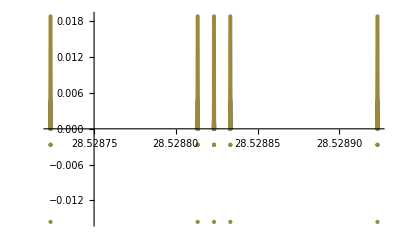

```mathematica
ListPlot[{evslo,evsmid,evshi},PlotRange->Full]
```

#### Testing Bisection Routine

```mathematica
BisectTest[F_,consts_,x0_,xf_,ϵ_]:=Module[{mid,val,lnegs,vam,mnegs,vah},
mid=x0+Abs[x0-xf]/2;
Print["Bisecting. Midpoint is "<>ToString[mid]];
val=F[x0,consts];
lnegs=CountNegs[val];
vam=F[mid,consts];
mnegs=CountNegs[vam];
If[xf-x0>ϵ,
bisects=Append[bisects,{{val[[1]],lnegs},{vam[[1]],mnegs}}];
If[lnegs<mnegs || (lnegs==mnegs && val[[1]] < vam[[1]]), (*if there is a zero on the lower half*)
Return[BisectTest[F,consts,x0,mid,ϵ]];, (*bisect it*)
Return[BisectTest[F,consts,mid,xf,ϵ]]; (*otherwise try the upper half*)
];,
vah = F[x0,consts];
Return[{mid,lnegs,CountNegs[vah]}];
]
]
```

```mathematica
newins[[35]]
```

{2,2283.02,28.5221,28.5533}

```mathematica
bisects={};
```

```mathematica
BisectTest[Critical,{0.1,newins[[35,2]],newins[[35,2]]/0.1},newins[[35,3]],newins[[35,4]],10^(-6)]
```

Bisecting. Midpoint is 28.5377

Bisecting. Midpoint is 28.5299

Bisecting. Midpoint is 28.526

Bisecting. Midpoint is 28.5279

$Aborted

### Data (evaluate me!)

```mathematica
lcs={{1,12.690344190457836},{2,12.689524383982643},{3,12.6891141270753},{1,19.775537554407492},{2,19.773917039623484},{3,19.77310855058022},{1,28.4309580035042},{2,28.428132182219997},{3,28.42672174726613},{1,38.65714240842499},{2,38.652617557672784},{3,38.65036114468239},{1,50.45449365139939},{2,50.44768833811395},{3,50.444298767251894},{1,63.82334306859411},{2,63.81358461291529},{3,63.80873155663721},{1,78.76398036791943},{2,78.75050342851318},{3,78.74381058220752},{1,95.27667281893082},{2,95.25861514895223},{3,95.2496616456192},{1,113.36167274531908},{2,113.3380695336964},{3,113.32638923660852},{1,133.0192236683797},{2,132.98900753981434},{3,132.97408621315844},{1,154.24956618831493},{2,154.2115601298865},{3,154.19283614610322},{1,177.05294082255568},{2,177.00585263001267},{3,176.9827144102892},{2,201.3720079708146},{3,201.34379318577703},{1,227.37976278236602},{2,227.31014622107614},{3,227.27614022011403},{1,284.00169473711867},{2,283.90284618304577},{3,283.8548953178106},{3,314.50142759794835},{1,346.9208710434614},{2,346.7849062484456},{3,346.71947693580296},{1,380.7426391033223},{2,380.58474809338804},{3,380.50910288875457},{1,416.1396027439041},{2,415.9572955298936},{3,415.87036471103784},{1,453.1120863078395},{2,452.90267532423604},{3,452.8033205346437},{1,491.6604345123051},{2,491.42101708438713},{1,531.7850119619397},{2,531.5124529820168},{3,531.3845506537473},{2,573.1771208100254},{3,573.032943150145},{2,616.4151616400341},{3,616.2532659458229},{2,661.2267199849011},{3,661.0455806151731},{2,707.6119473635918},{3,707.409947321401},{2,755.5709999114042},{3,755.3464291830314},{2,805.1040396742756},{3,804.8550877546659},{2,856.2112368090311},{3,855.9359877187526},{2,908.892766552628},{3,908.5891946853371},{2,963.1488120803842},{3,962.8147747282637}}
```

{{1,12.6903},{2,12.6895},{3,12.6891},{1,19.7755},{2,19.7739},{3,19.7731},{1,28.431},{2,28.4281},{3,28.4267},{1,38.6571},{2,38.6526},{3,38.6504},{1,50.4545},{2,50.4477},{3,50.4443},{1,63.8233},{2,63.8136},{3,63.8087},{1,78.764},{2,78.7505},{3,78.7438},{1,95.2767},{2,95.2586},{3,95.2497},{1,113.362},{2,113.338},{3,113.326},{1,133.019},{2,132.989},{3,132.974},{1,154.25},{2,154.212},{3,154.193},{1,177.053},{2,177.006},{3,176.983},{2,201.372},{3,201.344},{1,227.38},{2,227.31},{3,227.276},{1,284.002},{2,283.903},{3,283.855},{3,314.501},{1,346.921},{2,346.785},{3,346.719},{1,380.743},{2,380.585},{3,380.509},{1,416.14},{2,415.957},{3,415.87},{1,453.112},{2,452.903},{3,452.803},{1,491.66},{2,491.421},{1,531.785},{2,531.512},{3,531.385},{2,573.177},{3,573.033},{2,616.415},{3,616.253},{2,661.227},{3,661.046},{2,707.612},{3,707.41},{2,755.571},{3,755.346},{2,805.104},{3,804.855},{2,856.211},{3,855.936},{2,908.893},{3,908.589},{2,963.149},{3,962.815}}

```mathematica
leftovers={};
```

```mathematica
For[i=1,i≤Length[lcs],i++,
If[lcs[[i,1]]==1,
leftovers=Append[leftovers,i]
]
]
```

### Expanding Ranges (In-progress, do NOT evaluate)

This bit expands my ranges I'm searching in.

```mathematica
leftovers
```

{34,35,36,38,39,40,41,42,46,47,48,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96}

```mathematica
newins={};
```

```mathematica
For[i=1,i≤Length[leftovers],i++,
item=leftovers[[i]];
newins=Append[newins,{inputs[[item,1]],inputs[[item,2]],inputs[[item,3]]-1,inputs[[item,4]]+1,item}]
]
```

```mathematica
newins
```

{{1,40000.,176.223,181.189,34},{2,80000.,176.223,181.189,35},{3,160000.,176.223,181.189,36},{2,80000.,200.393,205.359,38},{3,160000.,200.393,205.359,39},{1,40000.,226.496,231.463,40},{2,80000.,226.496,231.463,41},{3,160000.,226.496,231.463,42},{1,40000.,283.537,288.504,46},{2,80000.,283.537,288.504,47},{3,160000.,283.537,288.504,48},{3,160000.,313.508,318.475,51},{1,40000.,346.379,351.346,52},{2,80000.,346.379,351.346,53},{3,160000.,346.379,351.346,54},{1,40000.,380.217,385.184,55},{2,80000.,380.217,385.184,56},{3,160000.,380.217,385.184,57},{1,40000.,415.988,420.955,58},{2,80000.,415.988,420.955,59},{3,160000.,415.988,420.955,60},{1,40000.,452.727,457.693,61},{2,80000.,452.727,457.693,62},{3,160000.,452.727,457.693,63},{1,40000.,491.398,496.365,64},{2,80000.,491.398,496.365,65},{3,160000.,491.398,496.365,66},{1,40000.,531.037,536.004,67},{2,80000.,531.037,536.004,68},{3,160000.,531.037,536.004,69},{1,40000.,572.609,577.576,70},{2,80000.,572.609,577.576,71},{3,160000.,572.609,577.576,72},{1,40000.,616.115,621.082,73},{2,80000.,616.115,621.082,74},{3,160000.,616.115,621.082,75},{1,40000.,661.555,666.521,76},{2,80000.,661.555,666.521,77},{3,160000.,661.555,666.521,78},{1,40000.,707.961,712.928,79},{2,80000.,707.961,712.928,80},{3,160000.,707.961,712.928,81},{1,40000.,755.334,760.301,82},{2,80000.,755.334,760.301,83},{3,160000.,755.334,760.301,84},{1,40000.,805.607,810.574,85},{2,80000.,805.607,810.574,86},{3,160000.,805.607,810.574,87},{1,40000.,856.848,861.814,88},{2,80000.,856.848,861.814,89},{3,160000.,856.848,861.814,90},{1,40000.,909.055,914.021,91},{2,80000.,909.055,914.021,92},{3,160000.,909.055,914.021,93},{1,40000.,963.195,968.162,94},{2,80000.,963.195,968.162,95},{3,160000.,963.195,968.162,96}}

```mathematica
Length[newins]
```

57

```mathematica
DistributeDefinitions[newins]
```

Only looking at first thru thirtieth here, just because. Could I guess do timing, don't actually give much of a shit.

```mathematica
addtllcs=ParallelTable[Findlc[newins[[i]],newins[[i,5]]],{i,1,30}]
```

***Beginning to calculate the 12th lambda, part 1

***Beginning to calculate the 12th lambda, part 3

***Beginning to calculate the 13th lambda, part 3

***Beginning to calculate the 14th lambda, part 2

***Beginning to calculate the 16th lambda, part 1

***Beginning to calculate the 16th lambda, part 3

***Beginning to calculate the 18th lambda, part 1

***Beginning to calculate the 18th lambda, part 3

Pass!

Bisecting. Midpoint is 178.706

Pass!

Bisecting. Midpoint is 348.862

Pass!

Bisecting. Midpoint is 286.021

Bisecting. Midpoint is 177.464

Bisecting. Midpoint is 284.779

Pass!

Bisecting. Midpoint is 228.979

Bisecting. Midpoint is 347.621

Bisecting. Midpoint is 176.844

Bisecting. Midpoint is 284.158

Bisecting. Midpoint is 177.154

Bisecting. Midpoint is 347.

Pass!

Bisecting. Midpoint is 348.862

Bisecting. Midpoint is 176.999

Bisecting. Midpoint is 283.848

Pass!

Bisecting. Midpoint is 178.706

Pass!

Bisecting. Midpoint is 202.876

Pass!

Bisecting. Midpoint is 286.021

Bisecting. Midpoint is 227.738

Bisecting. Midpoint is 346.689

Bisecting. Midpoint is 177.076

Bisecting. Midpoint is 284.003

Bisecting. Midpoint is 346.845

Bisecting. Midpoint is 177.038

Bisecting. Midpoint is 283.925

Bisecting. Midpoint is 227.117

Bisecting. Midpoint is 347.621

Bisecting. Midpoint is 346.922

Bisecting. Midpoint is 177.057

Bisecting. Midpoint is 283.964

Bisecting. Midpoint is 201.634

Bisecting. Midpoint is 346.883

Bisecting. Midpoint is 177.047

Bisecting. Midpoint is 177.464

Bisecting. Midpoint is 283.983

Bisecting. Midpoint is 346.903

Bisecting. Midpoint is 284.779

Bisecting. Midpoint is 227.427

Bisecting. Midpoint is 177.052

Bisecting. Midpoint is 283.993

Bisecting. Midpoint is 177.054

Bisecting. Midpoint is 346.912

Bisecting. Midpoint is 347.

Bisecting. Midpoint is 283.998

Bisecting. Midpoint is 177.053

Bisecting. Midpoint is 346.917

Bisecting. Midpoint is 227.272

Bisecting. Midpoint is 201.013

Bisecting. Midpoint is 284.

Bisecting. Midpoint is 346.92

Bisecting. Midpoint is 177.053

Bisecting. Midpoint is 176.844

Bisecting. Midpoint is 284.158

Bisecting. Midpoint is 177.053

Bisecting. Midpoint is 346.921

Bisecting. Midpoint is 284.002

Bisecting. Midpoint is 227.35

Bisecting. Midpoint is 346.689

Bisecting. Midpoint is 346.92

Bisecting. Midpoint is 284.002

Bisecting. Midpoint is 177.053

Bisecting. Midpoint is 284.002

Bisecting. Midpoint is 346.921

Bisecting. Midpoint is 201.324

Bisecting. Midpoint is 227.311

Bisecting. Midpoint is 177.053

Bisecting. Midpoint is 284.002

Bisecting. Midpoint is 346.921

Bisecting. Midpoint is 346.845

Bisecting. Midpoint is 177.053

Bisecting. Midpoint is 283.848

Bisecting. Midpoint is 284.002

Bisecting. Midpoint is 346.921

Bisecting. Midpoint is 177.154

Bisecting. Midpoint is 227.292

Bisecting. Midpoint is 177.053

Bisecting. Midpoint is 284.002

Bisecting. Midpoint is 346.921

Bisecting. Midpoint is 201.479

Bisecting. Midpoint is 177.053

Bisecting. Midpoint is 346.921

Bisecting. Midpoint is 284.002

Bisecting. Midpoint is 227.301

Bisecting. Midpoint is 346.767

Bisecting. Midpoint is 177.053

Bisecting. Midpoint is 346.921

Bisecting. Midpoint is 284.002

Bisecting. Midpoint is 177.053

Bisecting. Midpoint is 176.999

Bisecting. Midpoint is 284.003

Bisecting. Midpoint is 346.921

Bisecting. Midpoint is 284.002

Bisecting. Midpoint is 227.306

Bisecting. Midpoint is 177.053

Bisecting. Midpoint is 346.921

Bisecting. Midpoint is 201.401

Bisecting. Midpoint is 284.002

Bisecting. Midpoint is 346.728

Bisecting. Midpoint is 177.053

Bisecting. Midpoint is 227.309

Bisecting. Midpoint is 284.002

Bisecting. Midpoint is 346.921

Bisecting. Midpoint is 177.053

Bisecting. Midpoint is 346.921

Bisecting. Midpoint is 284.002

***Beginning to calculate the 12th lambda, part 2

Bisecting. Midpoint is 227.31

Bisecting. Midpoint is 283.925

Bisecting. Midpoint is 346.921

Bisecting. Midpoint is 284.002

Bisecting. Midpoint is 346.709

Bisecting. Midpoint is 176.921

Pass!

Bisecting. Midpoint is 178.706

***Beginning to calculate the 18th lambda, part 2

***Beginning to calculate the 16th lambda, part 2

Bisecting. Midpoint is 201.363

Bisecting. Midpoint is 227.31

Bisecting. Midpoint is 177.464

Pass!

Bisecting. Midpoint is 348.862

Bisecting. Midpoint is 346.718

Pass!

Bisecting. Midpoint is 286.021

Bisecting. Midpoint is 283.886

Bisecting. Midpoint is 176.844

Bisecting. Midpoint is 227.31

Bisecting. Midpoint is 176.96

Bisecting. Midpoint is 201.343

Bisecting. Midpoint is 347.621

Bisecting. Midpoint is 177.154

Bisecting. Midpoint is 284.779

Bisecting. Midpoint is 227.31

Bisecting. Midpoint is 346.723

Bisecting. Midpoint is 347.

Bisecting. Midpoint is 176.999

Bisecting. Midpoint is 283.867

Bisecting. Midpoint is 284.158

Bisecting. Midpoint is 176.979

Bisecting. Midpoint is 227.31

Bisecting. Midpoint is 201.353

Bisecting. Midpoint is 346.689

Bisecting. Midpoint is 177.076

Bisecting. Midpoint is 346.721

Bisecting. Midpoint is 283.848

Bisecting. Midpoint is 227.31

Bisecting. Midpoint is 346.845

Bisecting. Midpoint is 177.038

Bisecting. Midpoint is 176.989

Bisecting. Midpoint is 283.857

Bisecting. Midpoint is 201.348

Bisecting. Midpoint is 284.003

Bisecting. Midpoint is 227.31

Bisecting. Midpoint is 177.018

Bisecting. Midpoint is 346.72

Bisecting. Midpoint is 346.767

Bisecting. Midpoint is 283.925

Bisecting. Midpoint is 227.31

Bisecting. Midpoint is 177.008

Bisecting. Midpoint is 176.984

Bisecting. Midpoint is 346.806

Bisecting. Midpoint is 283.852

Bisecting. Midpoint is 201.346

Bisecting. Midpoint is 283.886

Bisecting. Midpoint is 346.719

Bisecting. Midpoint is 227.31

Bisecting. Midpoint is 177.004

Bisecting. Midpoint is 346.786

Bisecting. Midpoint is 283.906

Bisecting. Midpoint is 177.006

Bisecting. Midpoint is 176.982

Bisecting. Midpoint is 227.31

Bisecting. Midpoint is 346.719

Bisecting. Midpoint is 201.344

Bisecting. Midpoint is 346.777

Bisecting. Midpoint is 283.855

Bisecting. Midpoint is 283.896

Bisecting. Midpoint is 177.005

Bisecting. Midpoint is 227.31

Bisecting. Midpoint is 177.005

Bisecting. Midpoint is 346.781

Bisecting. Midpoint is 283.901

Bisecting. Midpoint is 176.983

Bisecting. Midpoint is 346.719

Bisecting. Midpoint is 227.31

Bisecting. Midpoint is 201.344

Bisecting. Midpoint is 283.856

Bisecting. Midpoint is 177.006

Bisecting. Midpoint is 283.903

Bisecting. Midpoint is 346.784

Bisecting. Midpoint is 176.982

Bisecting. Midpoint is 227.31

Bisecting. Midpoint is 346.719

Bisecting. Midpoint is 177.006

Bisecting. Midpoint is 283.902

Bisecting. Midpoint is 346.785

Bisecting. Midpoint is 201.344

***Beginning to calculate the 14th lambda, part 3

Bisecting. Midpoint is 177.006

Bisecting. Midpoint is 283.903

Bisecting. Midpoint is 283.855

Bisecting. Midpoint is 346.785

Bisecting. Midpoint is 346.719

Bisecting. Midpoint is 176.983

Bisecting. Midpoint is 177.006

Bisecting. Midpoint is 283.903

Bisecting. Midpoint is 346.785

Bisecting. Midpoint is 201.344

Pass!

Bisecting. Midpoint is 228.979

Bisecting. Midpoint is 177.006

Bisecting. Midpoint is 346.719

Bisecting. Midpoint is 283.903

Bisecting. Midpoint is 283.855

Bisecting. Midpoint is 346.785

Bisecting. Midpoint is 176.983

Bisecting. Midpoint is 177.006

Bisecting. Midpoint is 283.903

Bisecting. Midpoint is 346.785

Bisecting. Midpoint is 346.719

Bisecting. Midpoint is 177.006

Bisecting. Midpoint is 201.344

Bisecting. Midpoint is 227.738

Bisecting. Midpoint is 283.903

Bisecting. Midpoint is 283.855

Bisecting. Midpoint is 346.785

Bisecting. Midpoint is 177.006

Bisecting. Midpoint is 176.983

Bisecting. Midpoint is 346.719

Bisecting. Midpoint is 283.903

Bisecting. Midpoint is 346.785

Bisecting. Midpoint is 177.006

Bisecting. Midpoint is 201.344

Bisecting. Midpoint is 227.117

Bisecting. Midpoint is 177.006

Bisecting. Midpoint is 283.903

Bisecting. Midpoint is 176.983

Bisecting. Midpoint is 283.855

Bisecting. Midpoint is 346.785

Bisecting. Midpoint is 346.719

Bisecting. Midpoint is 177.006

### Analyzing data

```mathematica
leftovers
```

{1,4,7,10,13,16,19,22,25,28,31,34,39,42,46,49,52,55,58,60}

```mathematica
leftovers =Delete[leftovers,-2]
```

{1,4,7,10,13,16,19,22,25,28,31,34,39,42,46,49,52,55,60}

```mathematica
leftoverdelete=Table[{leftovers[[i]]},{i,1,Length[leftovers]}];
```

Removing incomplete data and null data

```mathematica
goodlcs=Delete[lcs,leftoverdelete]
```

{{2,12.6895},{3,12.6891},{2,19.7739},{3,19.7731},{2,28.4281},{3,28.4267},{2,38.6526},{3,38.6504},{2,50.4477},{3,50.4443},{2,63.8136},{3,63.8087},{2,78.7505},{3,78.7438},{2,95.2586},{3,95.2497},{2,113.338},{3,113.326},{2,132.989},{3,132.974},{2,154.212},{3,154.193},{2,177.006},{3,176.983},{2,201.372},{3,201.344},{2,227.31},{3,227.276},{2,283.903},{3,283.855},{3,314.501},{2,346.785},{3,346.719},{2,380.585},{3,380.509},{2,415.957},{3,415.87},{2,452.903},{3,452.803},{1,491.66},{2,491.421},{2,531.512},{3,531.385},{2,573.177},{3,573.033},{2,616.415},{3,616.253},{2,661.227},{3,661.046},{2,707.612},{3,707.41},{2,755.571},{3,755.346},{2,805.104},{3,804.855},{2,856.211},{3,855.936},{2,908.893},{3,908.589},{2,963.149},{3,962.815}}

All leftover goodlcs have enough data for error bars. Yay error bars!

```mathematica
Length[goodlcs]/2
```

30

```mathematica
goodlcs
```

{{2,12.6895},{3,12.6891},{2,19.7739},{3,19.7731},{2,28.4281},{3,28.4267},{2,38.6526},{3,38.6504},{2,50.4477},{3,50.4443},{2,63.8136},{3,63.8087},{2,78.7505},{3,78.7438},{2,95.2586},{3,95.2497},{2,113.338},{3,113.326},{2,132.989},{3,132.974},{2,154.212},{3,154.193},{2,177.006},{3,176.983},{2,201.372},{3,201.344},{2,227.31},{3,227.276},{2,283.903},{3,283.855},Null,{6,98928.8},{2,346.785},{3,346.719},{2,380.585},{3,380.509},{2,415.957},{3,415.87},{2,452.903},{3,452.803},{1,491.66},{2,491.421},{2,531.512},{3,531.385},{2,573.177},{3,573.033},{2,616.415},{3,616.253},{2,661.227},{3,661.046},{2,707.612},{3,707.41},{2,755.571},{3,755.346},{2,805.104},{3,804.855},{2,856.211},{3,855.936},{2,908.893},{3,908.589},{2,963.149},{3,962.815}}

```mathematica
goodlcs={{2,12.689524383982643},{3,12.6891141270753},{2,19.773917039623484},{3,19.77310855058022},{2,28.428132182219997},{3,28.42672174726613},{2,38.652617557672784},{3,38.65036114468239},{2,50.44768833811395},{3,50.444298767251894},{2,63.81358461291529},{3,63.80873155663721},{2,78.75050342851318},{3,78.74381058220752},{2,95.25861514895223},{3,95.2496616456192},{2,113.3380695336964},{3,113.32638923660852},{2,132.98900753981434},{3,132.97408621315844},{2,154.2115601298865},{3,154.19283614610322},{2,177.00585263001267},{3,176.9827144102892},{2,201.3720079708146},{3,201.34379318577703},{2,227.31014622107614},{3,227.27614022011403},{2,254.8203860449139},{3,254.77981941751204},{2,283.90284618304577},{3,283.8548953178106},{2,314.5576463358011},{3,314.50142759794835},{2,346.7849062484456},{3,346.71947693580296},{2,380.58474809338804},{3,380.50910288875457},{2,415.9572955298936},{3,415.87036471103784},{2,452.90267532423604},{3,452.8033205346437},{1,491.6604345123051},{2,491.42101708438713},{2,531.5124529820168},{3,531.3845506537473},{2,573.1771208100254},{3,573.032943150145},{2,616.4151616400341},{3,616.2532659458229},{2,661.2267199849011},{3,661.0455806151731},{2,707.6119473635918},{3,707.409947321401},{2,755.5709999114042},{3,755.3464291830314},{2,805.1040396742756},{3,804.8550877546659},{2,856.2112368090311},{3,855.9359877187526},{2,908.892766552628},{3,908.5891946853371},{2,963.1488120803842},{3,962.8147747282637}}
```

{{2,12.6895},{3,12.6891},{2,19.7739},{3,19.7731},{2,28.4281},{3,28.4267},{2,38.6526},{3,38.6504},{2,50.4477},{3,50.4443},{2,63.8136},{3,63.8087},{2,78.7505},{3,78.7438},{2,95.2586},{3,95.2497},{2,113.338},{3,113.326},{2,132.989},{3,132.974},{2,154.212},{3,154.193},{2,177.006},{3,176.983},{2,201.372},{3,201.344},{2,227.31},{3,227.276},{2,254.82},{3,254.78},{2,283.903},{3,283.855},{2,314.558},{3,314.501},{2,346.785},{3,346.719},{2,380.585},{3,380.509},{2,415.957},{3,415.87},{2,452.903},{3,452.803},{1,491.66},{2,491.421},{2,531.512},{3,531.385},{2,573.177},{3,573.033},{2,616.415},{3,616.253},{2,661.227},{3,661.046},{2,707.612},{3,707.41},{2,755.571},{3,755.346},{2,805.104},{3,804.855},{2,856.211},{3,855.936},{2,908.893},{3,908.589},{2,963.149},{3,962.815}}

Data for plotting/fitting will be in the form {{λc, error},{.....}}.

```mathematica
final=Table[{goodlcs[[i,2]],goodlcs[[i,2]]-goodlcs[[i+1,2]]},{i,1,60,2}]
```

{{12.6895,0.000410257},{19.7739,0.000808489},{28.4281,0.00141043},{38.6526,0.00225641},{50.4477,0.00338957},{63.8136,0.00485306},{78.7505,0.00669285},{95.2586,0.0089535},{113.338,0.0116803},{132.989,0.0149213},{154.212,0.018724},{177.006,0.0231382},{201.372,0.0282148},{227.31,0.034006},{254.82,0.0405666},{283.903,0.0479509},{314.558,0.0562187},{346.785,0.0654293},{380.585,0.0756452},{415.957,0.0869308},{452.903,0.0993548},{491.66,0.239417},{531.512,0.127902},{573.177,0.144178},{616.415,0.161896},{661.227,0.181139},{707.612,0.202},{755.571,0.224571},{805.104,0.248952},{856.211,0.275249}}

### Data from another sheet (evaluate!)

```mathematica
lls={{1,3.2344430923461918},{1,3.2304452896118168},{1,3.228457832336426},{2,7.201703071594238},{2,7.187644004821777},{2,7.180727005004883}};
```

```mathematica
valtimes={{18.371306000000004,0.8496356201171874},{36.80777399999988,0.844736328125},{25.82021900000018,0.843125},{118.79865699999982,0.8423217773437499},{148.38628600000038,0.8418432617187499},{122.87857900000017,0.8415234375},{199.06902100000025,0.8412939453125},{215.29059000000052,0.841123046875},{276.3703320000004,0.8409912109375001},{309.73127999999997,0.8408837890624999},{283.06138400000054,0.84080078125},{312.96907199999987,0.8407226562500001},{305.5294329999997,0.8406640624999999},{418.37500399999954,0.840615234375},{412.3826170000011,0.84056640625}};
```

### back to business

```mathematica
morevs=Table[{lls[[i+1,2]],lls[[i,2]]-lls[[i+1,2]]},{i,2,5,3}];
```

```mathematica
final=Join[morevs,final]
```

{{3.22846,0.00198746},{7.18073,0.006917},{12.6895,0.000410257},{19.7739,0.000808489},{28.4281,0.00141043},{38.6526,0.00225641},{50.4477,0.00338957},{63.8136,0.00485306},{78.7505,0.00669285},{95.2586,0.0089535},{113.338,0.0116803},{132.989,0.0149213},{154.212,0.018724},{177.006,0.0231382},{201.372,0.0282148},{227.31,0.034006},{254.82,0.0405666},{283.903,0.0479509},{314.558,0.0562187},{346.785,0.0654293},{380.585,0.0756452},{415.957,0.0869308},{452.903,0.0993548},{491.66,0.239417},{531.512,0.127902},{573.177,0.144178},{616.415,0.161896},{661.227,0.181139},{707.612,0.202},{755.571,0.224571},{805.104,0.248952},{856.211,0.275249}}

```mathematica
ev1={{valtimes[[7,2]],valtimes[[7,2]]-valtimes[[14,2]]}};
```

```mathematica
final=Join[ev1,final]
```

{{0.841294,0.000678711},{3.22846,0.00198746},{7.18073,0.006917},{12.6895,0.000410257},{19.7739,0.000808489},{28.4281,0.00141043},{38.6526,0.00225641},{50.4477,0.00338957},{63.8136,0.00485306},{78.7505,0.00669285},{95.2586,0.0089535},{113.338,0.0116803},{132.989,0.0149213},{154.212,0.018724},{177.006,0.0231382},{201.372,0.0282148},{227.31,0.034006},{254.82,0.0405666},{283.903,0.0479509},{314.558,0.0562187},{346.785,0.0654293},{380.585,0.0756452},{415.957,0.0869308},{452.903,0.0993548},{491.66,0.239417},{531.512,0.127902},{573.177,0.144178},{616.415,0.161896},{661.227,0.181139},{707.612,0.202},{755.571,0.224571},{805.104,0.248952},{856.211,0.275249}}

### Plots!

Information on data collection --n=1 had rho_inf = 700, drho = 0.01. n = 2 and 3 had rho_inf = 2000, drho = 0.1. n = 3 through 14 had rho_inf = 40,000 and drho = 0.1.

```mathematica
Needs["ErrorBarPlots`"];
```

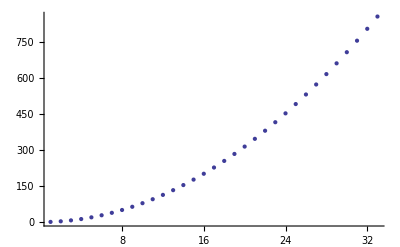

```mathematica
stuff = ErrorBarPlots`ErrorListPlot[final]
```

```mathematica
loglog=Table[{Log[2,N[i]],Log[2,final[[i,1]]]},{i,1,Length[final]}]
```

{{0.,-0.249318},{1.,1.69085},{1.58496,2.84413},{2.,3.66552},{2.32193,4.30547},{2.58496,4.82918},{2.80735,5.27241},{3.,5.65662},{3.16993,5.99568},{3.32193,6.29909},{3.45943,6.57364},{3.58496,6.82434},{3.70044,7.055},{3.80735,7.26859}}

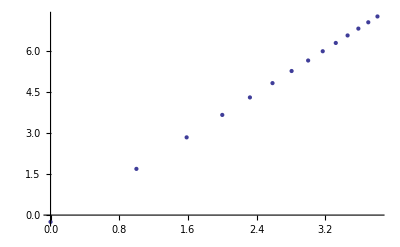

```mathematica
ListPlot[loglog]
```

```mathematica
fit=LinearModelFit[loglog,x,x]
```

FittedModel[-0.27899+1.97938 x]

```mathematica
fit["RSquared"]
```

0.99997

Linear wooooo!

```mathematica
f[x_] :=Normal[fit]
```

```mathematica
f[x]
```

-0.27899+1.97938 x

```mathematica
fit["ParameterErrors"]
```

{0.0088264,0.00314087}

```mathematica
Exp[-0.2789898192883946]
```

0.756548

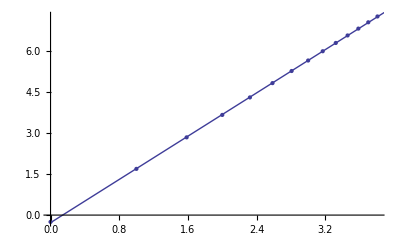

```mathematica
Show[ListPlot[loglog], Plot[f[x], {x, 0, 4}]]
```

### Weighted fit

final has data in the form {λc, Δλ} for n=1,2,3...

```mathematica
loglog=Table[{Log[N[i]],Log[final[[i,1]]],1/final[[i,1]]*final[[i,2]]},{i,1,Length[final]}]
```

{{0.,-0.172814,0.000806746},{0.693147,1.172,0.000615606},{1.09861,1.9714,0.000963273},{1.38629,2.54074,0.0000323314},{1.60944,2.98432,0.0000408883},{1.79176,3.34733,0.0000496165},{1.94591,3.65456,0.0000583801},{2.07944,3.92087,0.0000671943},{2.19722,4.15589,0.0000760563},{2.30259,4.3662,0.0000849952},{2.3979,4.5565,0.0000940004},{2.48491,4.73027,0.000103068},{2.56495,4.89015,0.000112212},{2.63906,5.0382,0.000121432}}

```mathematica
weights=Table[1/(loglog[[i,3]]^2),{i,1,Length[loglog]}]
```

{1.53648×10^6,2.63873×10^6,1.07771×10^6,9.56645×10^8,5.98138×10^8,4.06207×10^8,2.93407×10^8,2.2148×10^8,1.72874×10^8,1.38424×10^8,1.13172×10^8,9.41357×10^7,7.9418×10^7,6.7816×10^7}

```mathematica
Length[loglog]
```

14

Looking for form y = A + Bx.

```mathematica
Delta=Sum[weights[[i]],{i,Length[weights]}]*Sum[weights[[i]]*loglog[[i,1]]^2,{i,Length[loglog]}]-(Sum[weights[[i]]*loglog[[i,1]],{i,Length[loglog]}])^2;
```

```mathematica
x[i_]:=loglog[[i,1]];
y[i_]:=loglog[[i,2]];
w[i_]:=weights[[i]]; (*to make reading below easier*)
```

```mathematica
A=(Sum[w
[i]*x[i]^2,{i,14}]*Sum[w[i]*y[i],{i,14}]-Sum[w[i]*x[i],{i,14}]*Sum[w[i]*x[i]*y[i],{i,14}])/Delta
```

-0.221695

There’s the intercept.

```mathematica
B=(Sum[w
[i],{i,14}]*Sum[w[i]*x[i]*y[i],{i,14}]-Sum[w[i]*x[i],{i,14}]*Sum[w[i]*y[i],{i,14}])/Delta
```

1.99237

And the slope! Uncertainties:

```mathematica
σA=Sqrt[Sum[w[i]*x[i]^2,{i,14}]/Delta]
```

0.0000855332

```mathematica
σB=Sqrt[Sum[w[i],{i,14}]/Delta]
```

0.000046696

The fit still, at this point, appears not quite quadratic.

```mathematica
F[x_]:=A+B*x
```

```mathematica
fitvals=Table[F[loglog[[i,1]]],{i,1,14}];
```

```mathematica
Res=Table[fitvals[[i]]-loglog[[i,2]],{i,1,14}];
```

```mathematica
Table[Abs[Res[[i]]]<loglog[[i,3]],{i,1,14}]
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,False}

```mathematica
Res
```

{-0.0488813,-0.0126955,-0.0042557,-0.000430872,0.000574897,0.000819856,0.000718289,0.000448401,0.0000952925,-0.000297386,-0.000706179,-0.00111805,-0.00152571,-0.00192506}

```mathematica
fitvals
```

{-0.221695,1.15931,1.96714,2.54031,2.9849,3.34815,3.65527,3.92132,4.15599,4.3659,4.5558,4.72915,4.88863,5.03628}

```mathematica
Table[loglog[[i,2]],{i,1,14}]
```

{-0.172814,1.172,1.9714,2.54074,2.98432,3.34733,3.65456,3.92087,4.15589,4.3662,4.5565,4.73027,4.89015,5.0382}

```mathematica
Length[final]
```

33

```mathematica
test = Table[final[[i, 1]], {i, 1, 33}]
```

{0.841294,3.22846,7.18073,12.6895,19.7739,28.4281,38.6526,50.4477,63.8136,78.7505,95.2586,113.338,132.989,154.212,177.006,201.372,227.31,254.82,283.903,314.558,346.785,380.585,415.957,452.903,491.66,531.512,573.177,616.415,661.227,707.612,755.571,805.104,856.211}

```mathematica
FindFit[test, a*x^2, {a}, x]
```

{a→0.7863}

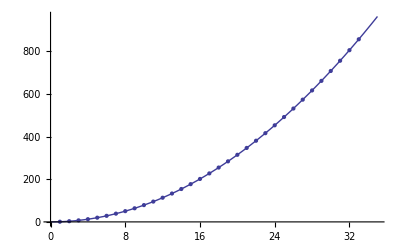

```mathematica
Show[Plot[.7863*x^2, {x, 0, 35}], stuff]
```